# Notebook 1: Monomorphic populations and adaptive dynamics Author: Mari Kawakatsu (marikawa@sas.upenn.edu)

## Part 1: Analysis with pDISC only

## 0. Setup for invasibility analysis with general pQ, pR

### Set up functions

```mathematica
Clear["Global`*"];

setupallequations[p_,q_, ua_,up_,nu1_]:=(
(*Clear[ua,up,eps,pgc,pgd,pbc,pbd,nsoln];*)
eps=(1-ua)*(1-up)+ua up;
nu2 = 1.0 - nu1;

A21 = A12;
A22 = A11;
B21 = B12;
B22 = B11;

(*fZR1=1.-fZQ1;
fZR2=1.-fZQ2;*)

(* observer view - donor intent - probgood *)
pgc=eps;
pgd=ua;
pbc=p(eps-ua)+q(1-eps-ua)+ua;
pbd=q(1-2ua)+ua;

(* generation equations for reputation relations *)
g11Z=fZQ1 g11ZQ + (1.-fZQ1) g11ZR;
g12Z=fZQ1 g12ZQ + (1.-fZQ1) g12ZR;
g21Z=fZQ2 g21ZQ + (1.-fZQ2) g21ZR;
g22Z=fZQ2 g22ZQ + (1.-fZQ2) g22ZR;

gbul1 = nu1 g11Z + nu2 g21Z;
gbul2 = nu1 g12Z + nu2 g22Z;
gstar1 = nu1 g11S  + nu2 g21S;
gstar2 = nu1 g12S  + nu2 g22S;

g11a1 = nu1 (fZQ1 g11ZQ g11ZQ +(1.-fZQ1) g11ZR g11ZR) + nu2(fZQ2 g21ZQ g11ZQ +(1.-fZQ2) g21ZR g21ZR);
g11b1 = gbul1 - g11a1;
g11c1 = gbul1 - g11a1;
g11d1 = 1 - gbul1 - gbul1 + g11a1;
g12a1 = nu1 (fZQ1 g12ZQ g11ZQ + (1.-fZQ1) g12ZR g11ZR)+ nu2 (fZQ2 g22ZQ g21ZQ + (1.-fZQ2) g22ZR g21ZR);
g12b1 = gbul2 - g12a1;
g12c1 = gbul1 - g12a1;
g12d1 = 1 - gbul2 - gbul1 + g12a1;
g21a1 = nu1(fZQ1 g11ZQ g12ZQ + (1.-fZQ1) g11ZR g12ZR)+ nu2 (fZQ2 g21ZQ g22ZQ + (1.-fZQ2)g21ZR g22ZR);
g21b1 = gbul1 - g21a1;
g21c1 = gbul2 - g21a1;
g21d1 = 1 - gbul1 - gbul2 + g21a1;
g22a1 =  nu1(fZQ1 g12ZQ g12ZQ +  (1.-fZQ1) g12ZR g12ZR)+ nu2 (fZQ2 g22ZQ g22ZQ + (1.-fZQ2) g22ZR g22ZR);
g22b1 = gbul2 - g22a1;
g22c1 = gbul2 - g22a1;
g22d1 = 1 - gbul2 - gbul2 + g22a1;
g11a2 = nu1 g11S g11Z + nu2 g21S g21Z;
g11b2 = gbul1 - g11a2;
g11c2 = gstar1 - g11a2;
g11d2 = 1 - gbul1 - gstar1 + g11a2;
g12a2 = nu1 g12S g11Z + nu2 g22S g21Z;
g12b2 = gbul2 - g12a2;
g12c2 = gstar1 - g12a2;
g12d2 = 1 - gbul2 - gstar1 + g12a2;
g21a2 = nu1 g11S g12Z + nu2 g21S g22Z;
g21b2 = gbul1 - g21a2;
g21c2 = gstar2 - g21a2;
g21d2 = 1 - gbul1 - gstar2 + g21a2;
g22a2 = nu1 g12S g12Z + nu2 g22S g22Z;
g22b2 = gbul2 - g22a2;
g22c2 = gstar2 - g22a2;
g22d2 = 1 - gbul2 - gstar2 + g22a2;
g11a3 = nu1 g11Z g11S + nu2 g21Z g21S;
g11b3 = gstar1 - g11a3;
g11c3 = gbul1 - g11a3;
g11d3 = 1 - gstar1 - gbul1 + g11a3;
g12a3 = nu1 g12Z g11S + nu2 g22Z g21S;
g12b3 = gstar2 - g12a3;
g12c3 = gbul1 - g12a3;
g12d3 = 1 - gstar2 - gbul1 + g12a3;
g21a3 = nu1 g11Z g12S + nu2 g21Z g22S;
g21b3 = gstar1 - g21a3;
g21c3 = gbul2 - g21a3;
g21d3 = 1 - gstar1 - gbul2 + g21a3;
g22a3 = nu1 g12Z g12S + nu2 g22Z g22S;
g22b3 = gstar2 - g22a3;
g22c3 = gbul2 - g22a3;
g22d3 = 1 - gstar2 - gbul2 + g22a3;
g11a4 = nu1 g11S g11S + nu2 g21S g21S;
g11b4 = gstar1 - g11a4;
g11c4 = gstar1 - g11a4;
g11d4 = 1 - gstar1 - gstar1 + g11a4;
g12a4 = nu1 g12S g11S + nu2 g22S g21S;
g12b4 = gstar2 - g12a4;
g12c4 = gstar1 - g12a4;
g12d4 = 1 - gstar2 - gstar1 + g12a4;
g21a4 = nu1 g11S g12S + nu2 g21S g22S;
g21b4 = gstar1 - g21a4;
g21c4 = gstar2 - g21a4;
g21d4 = 1 - gstar1 - gstar2 + g21a4;
g22a4 = nu1 g12S g12S + nu2 g22S g22S;
g22b4 = gstar2 - g22a4;
g22c4 = gstar2 - g22a4;
g22d4 = 1 - gstar2 - gstar2 + g22a4;

g11Zpriv=g11a1 pgc + g11b1 pgd + g11c1 pbc + g11d1 pbd;
g12Zpriv=g12a1 pgc + g12b1 pgd + g12c1 pbc + g12d1 pbd;
g21Zpriv=g21a1 pgc + g21b1 pgd + g21c1 pbc + g21d1 pbd;
g22Zpriv=g22a1 pgc + g22b1 pgd + g22c1 pbc + g22d1 pbd;
g11Zpub=gbul1 pgc + (1-gbul1)pbd;
g12Zpub=gbul2 pgc + (1-gbul2)pbd;
g21Zpub=gbul1 pgc + (1-gbul1)pbd;
g22Zpub=gbul2 pgc + (1-gbul2)pbd;
g11Zind=g11a2 pgc + g11b2 pgd + g11c2 pbc + g11d2 pbd;
g12Zind=g12a2 pgc + g12b2 pgd + g12c2 pbc + g12d2 pbd;
g21Zind=g21a2 pgc + g21b2 pgd + g21c2 pbc + g21d2 pbd;
g22Zind=g22a2 pgc + g22b2 pgd + g22c2 pbc + g22d2 pbd;
g11SZind=g11a3 pgc + g11b3 pgd + g11c3 pbc + g11d3 pbd;
g12SZind=g12a3 pgc + g12b3 pgd + g12c3 pbc + g12d3 pbd;
g21SZind=g21a3 pgc + g21b3 pgd + g21c3 pbc + g21d3 pbd;
g22SZind=g22a3 pgc + g22b3 pgd + g22c3 pbc + g22d3 pbd;
g11SZpriv=g11a4 pgc + g11b4 pgd + g11c4 pbc + g11d4 pbd;
g12SZpriv=g12a4 pgc + g12b4 pgd + g12c4 pbc + g12d4 pbd;
g21SZpriv=g21a4 pgc + g21b4 pgd + g21c4 pbc + g21d4 pbd;
g22SZpriv=g22a4 pgc + g22b4 pgd + g22c4 pbc + g22d4 pbd;
g11SZpub=gstar1 pgc +(1-gstar1) pbd;
g12SZpub=gstar2 pgc +(1-gstar2) pbd;
g21SZpub=gstar1 pgc +(1-gstar1) pbd;
g22SZpub=gstar2 pgc +(1-gstar2) pbd;

(*probability that individuals in each group uses reputations / stereotypes*)
pIndiv1=fZQ1(1-pQ)+(1-fZQ1)(1-pR);
pStype1=fZQ1 *pQ+(1-fZQ1)pR;
pIndiv2=fZQ2(1-pQ)+(1-fZQ2)(1-pR);
pStype2=fZQ2 *pQ+(1-fZQ2)pR;

(* general equation to solve for equilibrium reputations; we use FindRoot which is fast but requires initial guess *)
ng11Z := g11Z;
ng12Z := g12Z;
ng21Z := g21Z ;
ng22Z := g22Z ;
ng11S := g11S;
ng12S := g12S;
ng21S := g21S;
ng22S := g22S;

(* cooperation levels *)
coop11[pstar_,upp_] :=(1-upp)*((1-pstar) ng11Z + pstar ng11S);
coop12[pstar_,upp_] :=(1-upp)*((1-pstar) ng21Z + pstar ng21S);
coop21[pstar_,upp_] :=(1-upp)*((1-pstar)ng12Z + pstar ng12S);
coop22[pstar_,upp_] :=(1-upp)*((1-pstar) ng22Z + pstar ng22S);
coopavg[pstar_,upp_]:=(coop11[pstar,upp]+coop12[pstar,upp])/2
)

(* Manually compute the root using the secant method *)
(*Clear[secantmethod,edgecheck,findsingularpoints, offsetparam];*)
secantmethod[f_,x0_,x1_,tol_:10^-10,iter_:50,stepbystep_:False]:=Module[{fx0,fx1,fx2,xx0,xx1,xx2,dir,i},
xx0=x0;
xx1=x1;
fx0=N@Evaluate[f[xx0]];
fx1=N@Evaluate[f[xx1]];
If[stepbystep==True,Print["start from: x0 = ",xx0,", x1 = ",xx1]];
(* check that we haven't found the root yet *)
If[Abs[fx0]<tol&&Abs[fx1]>tol,
If[stepbystep==True,Print["\tYou already found the root at x = ",xx0,", where f(x0) = ",fx0,". f(x0+tol) = ",N@Evaluate[f[xx0+tol]]]];
dir=If[N@Evaluate[f[xx0+tol]]>fx0,"increase","decrease"];
Return[{xx0,dir}]
];
If[Abs[fx1]<tol&&Abs[fx0]>tol,
If[stepbystep==True,Print["\tYou already found the root at x = ",xx1,", where f(x1) = ",fx1,". f(x1-tol) = ",N@Evaluate[f[xx1-tol]]]];
dir=If[N@Evaluate[f[xx1-tol]]<fx1,"increase","decrease"];
Return[{xx1,dir}]
];
(* check that f(x0) and f(x1) have different signs *)
If[fx0*fx1>=0,
If[stepbystep==True,Print["\tNeed f(x0)*f(x1)<0; check x0 and x1 values"]];Return[]];
(* iteratively find root *)
i=0;
While[i<=iter,
(* update guessed root *)
xx2=(xx0*fx1-xx1*fx0)/(fx1-fx0);
fx2=N@Evaluate[f[xx2]];
If[Abs[fx2]<tol,
(* found the root *)
If[stepbystep==True,Print["\tFound root x = ",xx2," after ",i," iterations"]];
dir=If[fx1>fx0,"increase","decrease"];
Return[{xx2,dir}],
(* haven't found the root; update x0 and x1 *)
If[stepbystep==True,Print["\titeration ",i,": f(",xx0,") = ",fx0,", f(",xx1,") = ",fx1]];
If[fx0*fx2>0,xx0=xx2;fx0=fx2,
If[fx1*fx2>0,xx1=xx2;fx1=fx2,Print["!!! check x values !!!: x0 = ",xx0,", x1 = ",xx1,", x2 = ",xx2]]
];
i++
];
]
]

offsetparam=10.^4;

edgecheck[f_,xmin_:0.,xmax_:1.,tol_:10^-10,stepbystep_:False]:=Module[{mindir,maxdir,fxmin,fxmax,fxminδ,fxmaxδ},
(*fxmin=N@Evaluate[f[xmin]];*)(*version for sweeping pQ=0*)
(*fxmax=N@Evaluate[f[xmin]];*)(*version for sweeping pQ=0*)
(*fxminδ=f[xmin+tol];*)(*version for sweeping pQ=0*)
(*fxmaxδ=f[xmax-tol];*)(*version for sweeping pQ=0*)
fxmin=0.;fxmax=0; (*version for sweeping just below*)
fxminδ=f[xmin+offsetparam*tol];
fxmaxδ=f[xmax-offsetparam*tol];

mindir=If[fxmin<fxminδ,"increase","decrease"];
maxdir=If[fxmaxδ<fxmax,"increase","decrease"];
If[stepbystep==True,
(*Print[{{xmin,fxmin,fxminδ},{xmax,fxmaxδ,fxmax}}];*)
Print["At xmin = ",xmin,", f(xmin) = ",fxmin,", whereas f(xmin+tol) = ",fxminδ];
Print["At xmax = ",xmax,", f(xmax) = ",fxmax,", whereas f(xmax-tol) = ",fxmaxδ];
Print[{{xmin,mindir},{xmax,maxdir}}];
];
Return[{{xmin,mindir},{xmax,maxdir}}]
]

findsingularpoints[f_,xmin_:0.,xmax_:1.,xintervals_:10,tol_:10^-10,iter_:50,stepbystep_:False,param_:Null]:=Module[{breaks,sol,sollist,soltable,edgesol},
(*search for intermediate singular points*)
If[stepbystep==True,Print[Information@f]];
sollist={};
breaks=Sort@Flatten@{N@Subdivide[xmin+tol*offsetparam,xmax-tol*offsetparam,xintervals],0.01,0.99}; (*x=0 and 1 are checked by edgecheck*)
(*If[AllTrue[breaks,(Abs[f[#]]<tol&)]&&AllTrue[{0.,1.},(Abs[f[#]]<tol&)],*)(*version for sweeping pQ=0*)
If[AllTrue[breaks,(Abs[f[#]]<tol&)],
(*if f evaluated at all initial points for the secand method and the edge values, raise a flag*)
If[stepbystep==True,Print["f is zero at all break values; likely a neutral case. Check param = ",param]];
sollist={}, (*redundant but making explicit*)
(*otherwise*)
If[stepbystep==True,Print[breaks]];
soltable=Table[
sol=secantmethod[f,breaks[[j]],breaks[[j+1]],tol,iter,stepbystep];
sollist=AppendTo[sollist,sol];
{breaks[[j]],breaks[[j+1]],sol},
{j,1,xintervals+2}
];
If[stepbystep==True,Print[soltable//MatrixForm]];
(*check edge cases*)
edgesol=edgecheck[f,xmin,xmax,tol,stepbystep];
sollist=Last@(AppendTo[sollist,#]&/@edgesol);
(*select unique elements*)
If[stepbystep==True,Print[sollist]];
(*first, check if there are any neighboring intermediate points*)
sollist=DeleteDuplicates[Sort@Cases[Chop[N@sollist,tol*offsetparam],{_?NumericQ,_}],(#1[[2]]==#2[[2]]&&Abs[#1[[1]]-#2[[1]]]<tol*offsetparam)&]; 
(*then check edgees*)
sollist=DeleteDuplicates[sollist,((#1[[1]]==0.||#1[[2]]==0.)&&#1[[2]]==#2[[2]]&&Abs[#1[[1]]-#2[[1]]]<tol*offsetparam*1.01)&]; (*check 0*)
sollist=DeleteDuplicates[Reverse@sollist,((#1[[1]]==1.||#1[[2]]==1.)&&#1[[2]]==#2[[2]]&&Abs[#1[[1]]-#2[[1]]]<tol*offsetparam*1.01)&]; (*check 1*)
];
If[stepbystep==True,Print[sollist]];
Return[sollist]
]
```

### Set norm

```mathematica
Clear[nu];nu=.5;
norm="SJ";setupallequations[0,1, ua,up,nu]
(*norm="SS";setupallequations[1,1, ua,up,nu]*)
(*norm="SC";setupallequations[1,0, ua,up,nu]*)
(*norm="SH";setupallequations[0,0, ua,up,nu]*)
```

### Invasibility conditions

Solve for equilibrium reputations:

```mathematica
(*full version*)
nsoln[pQQ_,pRR_,uaa_,upp_,Atype_, Btype_,fZQ_] :=Module[{A11,A12,B11,B12,A21,A22,B21,B22},
A11 = KroneckerDelta[Atype, 1] + KroneckerDelta[Atype, 2];
A12 = KroneckerDelta[Atype, 2];
B11 = KroneckerDelta[Btype, 1] + KroneckerDelta[Btype, 2];
B12 = KroneckerDelta[Btype, 2];
A21 = A12;
A22 = A11;
B21 = B12;
B22 = B11;

FindRoot[{
g11ZQ == (1-pQ)((1 - A11)g11Zpriv+ A11 g11Zpub)+pQ* g11Zind,
g12ZQ == (1-pQ) ((1 - A21)g12Zpriv+ A21 g12Zpub)+pQ* g12Zind,
g21ZQ == (1-pQ)((1 - A12)g21Zpriv+ A12 g21Zpub)+pQ* g21Zind,
g22ZQ == (1-pQ) ((1 - A22)g22Zpriv+ A22 g22Zpub)+pQ* g22Zind,
g11ZR == (1-pR)((1 - A11)g11Zpriv+ A11 g11Zpub)+pR* g11Zind,
g12ZR == (1-pR) ((1 - A21)g12Zpriv+ A21 g12Zpub)+pR* g12Zind,
g21ZR == (1-pR)((1 - A12)g21Zpriv+ A12 g21Zpub)+pR* g21Zind,
g22ZR == (1-pR) ((1 - A22)g22Zpriv+ A22 g22Zpub)+pR* g22Zind,
g11S == pIndiv1  g11SZind+ pStype1 ((1 - B11)g11SZpriv+ B11 g11SZpub),
g12S == pIndiv1  g12SZind+ pStype1 ((1 - B21)g12SZpriv+ B21 g12SZpub),
g21S == pIndiv2  g21SZind+ pStype2 ((1 - B12)g21SZpriv+ B12 g21SZpub),
g22S == pIndiv2  g22SZind+ pStype2 ((1 - B22)g22SZpriv+ B22 g22SZpub)
}/.{ ua->uaa, up->upp,fZQ1->fZQ,fZQ2->fZQ,pQ->pQQ,pR->pRR},{{g11ZQ,.49},{g12ZQ,.49},{g21ZQ,.49},{g22ZQ,.49},
{g11ZR,.49},{g12ZR,.49},{g21ZR,.49},{g22ZR,.49},
{g11S,.49},{g12S,.49},{g21S,.49},{g22S,.49}
}
]
]
```

Z_Q can invade Z_R iff the following quantity evaluated at f_Q=0 is greater than zero:

```mathematica
(*updated 220329*)
canZQinvadeZR[pQQ_, pRR_,uaa_,upp_,Atype_,Btype_,nu1_,a_,b_,c_]:=Module[{A11,A12,B11,B12,A21,A22,B21,B22,Δg11ZQR,Δg12ZQR,Δg21ZQR,Δg22ZQR},
A11 = KroneckerDelta[Atype, 1] + KroneckerDelta[Atype, 2];
A12 = KroneckerDelta[Atype, 2];
B11 = KroneckerDelta[Btype, 1] + KroneckerDelta[Btype, 2];
B12 = KroneckerDelta[Btype, 2];
A21 = A12;
A22 = A11;
B21 = B12;
B22 = B11;
Δg11ZQR=(pRR-pQQ)((1 - A11)g11Zpriv+ A11 g11Zpub)+(pQQ-pRR)g11Zind/.{ ua->uaa, up->upp,pQ->pQQ,pR->pRR};
Δg12ZQR=(pRR-pQQ)((1 - A12)g12Zpriv+ A12 g12Zpub)+(pQQ-pRR)g12Zind/.{ ua->uaa, up->upp,pQ->pQQ,pR->pRR};
Δg21ZQR=(pRR-pQQ)((1 - A21)g21Zpriv+ A21 g21Zpub)+(pQQ-pRR)g21Zind/.{ ua->uaa, up->upp,pQ->pQQ,pR->pRR};
Δg22ZQR=(pRR-pQQ)((1 - A22)g22Zpriv+ A22 g22Zpub)+(pQQ-pRR)g22Zind/.{ ua->uaa, up->upp,pQ->pQQ,pR->pRR};

(1-upp)*(b(1-pRR)(nu1^2 Δg11ZQR+nu1(1-nu1)Δg12ZQR+(1-nu1)nu1 Δg21ZQR+(1-nu1)^2 Δg22ZQR)-(pQQ-pRR)(c(nu1(gstar1-gbul1)+(1-nu1)(gstar2-gbul2))))+a(pQQ-pRR)/.{fZQ1->0.,fZQ2->0.}
]
```

```mathematica
(*UniqueElements[lst_]:=Select[Tally[lst],#[[2]]==1&][[All,1]]*)
Qvals[pR_,step_]:={0.,step,Max[pR-step,0],pR,Min[pR+step,1.],1.-step,1.};
```

### Options for plotting and exporting files

```mathematica
(* lable formatting *)
types={"private","group-wise","public"};
typelabel[Atype_,Btype_]:=StringJoin["Individual reputations ",ToString[Style[types[[Atype+1]],Bold],StandardForm],",\nstereotyped reputations ",ToString[Style[types[[Btype+1]],Bold],StandardForm]];
typelabelrep[Atype_,Btype_]:=StringJoin["Individual reputations \n",ToString[Style[types[[Atype+1]],Bold],StandardForm]];
typelabelstereo[Atype_,Btype_]:=StringJoin["Stereotyped reputations \n",ToString[Style[types[[Btype+1]],Bold],StandardForm]];
typelabeldiag[Atype_,Btype_]:=If[Atype==Btype,StringJoin["Individual & stereotyped\n reputations ",ToString[Style[types[[Atype+1]],Bold],StandardForm]],Print["Check Atype and Btype"]];

(* plot theme *)
Themes`AddThemeRules["theme_mk",
LabelStyle->Directive[10,Black],
Axes->False,
Frame->True,
FrameStyle->{{Black,White},{Black,White}},
FrameTicks->{
{({#,Style[PaddedForm[#,{1,1}],10,Black],{0,0.02}}&)/@Subdivide[0.,1.,5],({#,Style[PaddedForm[#,{1,1}],6,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]},
{({#,Style[PaddedForm[#,{1,1}],10,Black],{0,0.02}}&)/@Subdivide[0.,1.,5],({#,Style[PaddedForm[#,{1,1}],12,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]}
},
Background->White,
InterpolationOrder->0,
IntervalMarkers->"Bands",
IntervalMarkersStyle->Thickness[10^-6],
ColorFunctionScaling->False,
AspectRatio->1,
PlotRangeClipping->False,
LegendLabel->Black,
FillingStyle->Opacity[0.1]
];
$PlotTheme="theme_mk";

SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"];
SetOptions[SelectedNotebook[],PrintPrecision->10];

(* directory *)
directory=NotebookDirectory[]<>"plots/";
```

### Check setup

```mathematica
(*directory*)
norm
```

SJ

## 1. Cooperation levels in monomorphic pDISC populations (Figures 2, S2-S4)

### Define functions

```mathematica
Clear[coopinoutmonomorphic,coopinoutmonomorphic2,coopcolors];
Clear[repsinoutmonomorphic];

(*plot in-group/out-group cooperation levels in a monomorphic population of pDISC, varying p*)
coopcolors = {RGBColor["#664148"],RGBColor["#A98189"],RGBColor["#E1D5D7"]};
coopcolors = {RGBColor["#9B5D32"],RGBColor["#CA9C78"],RGBColor["#EFDAB6"]};
coopcolors = {RGBColor["#001465"],RGBColor["#3b5898"],RGBColor["#829ec3"]}; (*navy, blue, light blue*)
coopcolors = {RGBColor["#001350"],RGBColor["#375e94"],RGBColor["#81AFD3"]}; (*navy, blue, light blue*)
coopcolors = {RGBColor["#0f4880"],RGBColor["#1e90ff"],RGBColor["#8FC8FF"]}; (*navy, blue, light blue*)
(*updated with a better grid*)
coopinoutmonomorphic[ua_,up_]:=
Legended[Labeled[Grid[Table[
Plot[
{coop11[rr,up] /.{fZQ1->0.,fZQ2->0.}/. nsoln[rr,rr,ua,up,Ai, Bi,0],
coopavg[rr,up] /.{fZQ1->0.,fZQ2->0.}/. nsoln[rr,rr,ua,up,Ai, Bi,0],coop12[rr,up] /.{fZQ1->0.,fZQ2->0.}/. nsoln[rr,rr,ua,up,Ai, Bi,0]},
 {rr,0,1},
PlotStyle->{{coopcolors[[1]],Dashed,Thickness[0.015]},{coopcolors[[2]],Opacity[0.85],Thickness[0.015]},{coopcolors[[3]],Dashed,Thickness[0.015]}},
PlotRange->{0,1},
PlotRangePadding->0.05,
ImageSize->Automatic->{100,100},
ImagePadding->{{If[Bi==2,25,60],60},{If[Ai==0,25,60],If[Ai==2,80,60]}},
FrameLabel->{{None,Style[Framed[Rotate[typelabelrep[Ai,Bi],-π]],Black]},{None,Style[Framed@typelabelstereo[Ai,Bi],Black]}},
Epilog->Inset[Style[ToUpperCase@FromLetterNumber[3*(2-Ai)+(2-Bi)+1],16],Offset[{0,0},Scaled[{-0.15,1.13}]]]
],
{Ai,{2,1,0}},{Bi, {2,1,0}}
],
Spacings->{-6.25,-6.25}
],
{Style["Cooperation level          ",18,Black],Style["Stereotype-use propensity (p)       ",18,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],
LineLegend[{{coopcolors[[1]],Dashed},Directive@{coopcolors[[2]],Opacity[0.85]},{coopcolors[[3]],Dashed}},{"in-group\ncooperation","average\ncooperation","out-group\ncooperation"}]
]
(*plot in-group/out-group cooperation levels in a monomorphic population of pDISC, varying ua*)
coopinoutmonomorphic2[p_,up_]:=
Legended[Labeled[Grid[Table[
Plot[
{coop11[p,up] /.{fZQ1->0.,fZQ2->0.}/. nsoln[p,p,ua,up,Ai, Bi,0],
coopavg[p,up] /.{fZQ1->0.,fZQ2->0.}/. nsoln[p,p,ua,up,Ai, Bi,0],
coop12[p,up] /.{fZQ1->0.,fZQ2->0.}/. nsoln[p,p,ua,up,Ai, Bi,0]},
 {ua,0,0.5},
PlotStyle->{{coopcolors[[1]],Dashed,Thickness[0.015]},{coopcolors[[2]],Opacity[0.85],Thickness[0.015]},{coopcolors[[3]],Dashed,Thickness[0.015]}},
PlotRange->{0,1},
PlotRangePadding->0.05,
FrameTicks->{({#,#,{0,0.02}}&)/@Subdivide[0.,0.5,5],({#,#,{0,0.02}}&)/@Subdivide[0.,1.,5]},
ImageSize->{150,150},
PlotLabel->Style[typelabel[Ai,Bi],8]
],
{Ai,{2,1,0}},{Bi, {2,1,0}}
],
Spacings->{-1, Automatic}
],
{Style["Cooperation level",18,Black],Style["      Assessment error rate (u_a)",18,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],
LineLegend[{{coopcolors[[1]],Dashed},Directive@{coopcolors[[2]],Opacity[0.85]},{coopcolors[[3]],Dashed}},{"in-group\ncooperation","average\ncooperation","out-group\ncooperation"}]
]
(*plot in-group/out-group reputation and stereotype levels in a monomorphic population of pDISC, varying p*)
repsinoutmonomorphic[ua_,up_]:=
Legended[Labeled[Grid[Table[
Plot[
{ng11Z /.{fZQ1->0.,fZQ2->0.}/. nsoln[rr,rr,ua,up,Ai, Bi,0],
ng12Z /.{fZQ1->0.,fZQ2->0.}/. nsoln[rr,rr,ua,up,Ai, Bi,0],
ng11S /.{fZQ1->0.,fZQ2->0.}/. nsoln[rr,rr,ua,up,Ai, Bi,0],
ng12S /.{fZQ1->0.,fZQ2->0.}/. nsoln[rr,rr,ua,up,Ai, Bi,0]},
 {rr,0,1},
PlotStyle->{{RGBColor["#810f7c"],Opacity[0.75]},{RGBColor["#810f7c"],Dashed},{RGBColor["#8c96c6"],Opacity[0.75]},{RGBColor["#8c96c6"],Dashed}},
PlotRange->{0,1},
PlotRangePadding->0.05,
(*Frame->True,
FrameStyle->{{Black,White},{Black,White}},*)
ImageSize->Automatic->{100,100},
ImagePadding->{{If[Bi==2,25,60],60},{If[Ai==0,25,60],If[Ai==2,80,60]}},
FrameLabel->{{None,Style[Framed[Rotate[typelabelrep[Ai,Bi],-π]],Black]},{None,Style[Framed@typelabelstereo[Ai,Bi],Black]}},
Epilog->Inset[Style[ToUpperCase@FromLetterNumber[3*(2-Ai)+(2-Bi)+1],16],Offset[{0,0},Scaled[{-0.15,1.13}]]]
],
{Ai,{2,1,0}},{Bi, {2,1,0}}
],
Spacings->{-6.25,-6.25}
],
{Style["Average reputation     ",18,Black],Style["Stereotype-use propensity (p)       ",18,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],
LineLegend[{Directive@{RGBColor["#810f7c"],Opacity[0.75]},{RGBColor["#810f7c"],Dashed},{RGBColor["#8c96c6"],Opacity[0.75]},{RGBColor["#8c96c6"],Dashed}},{"in-group\nindividual rep.","out-group\nindividual rep.","in-group\nstereotyped rep.","out-group\nstereotyped rep."}]
]
```

### Plots

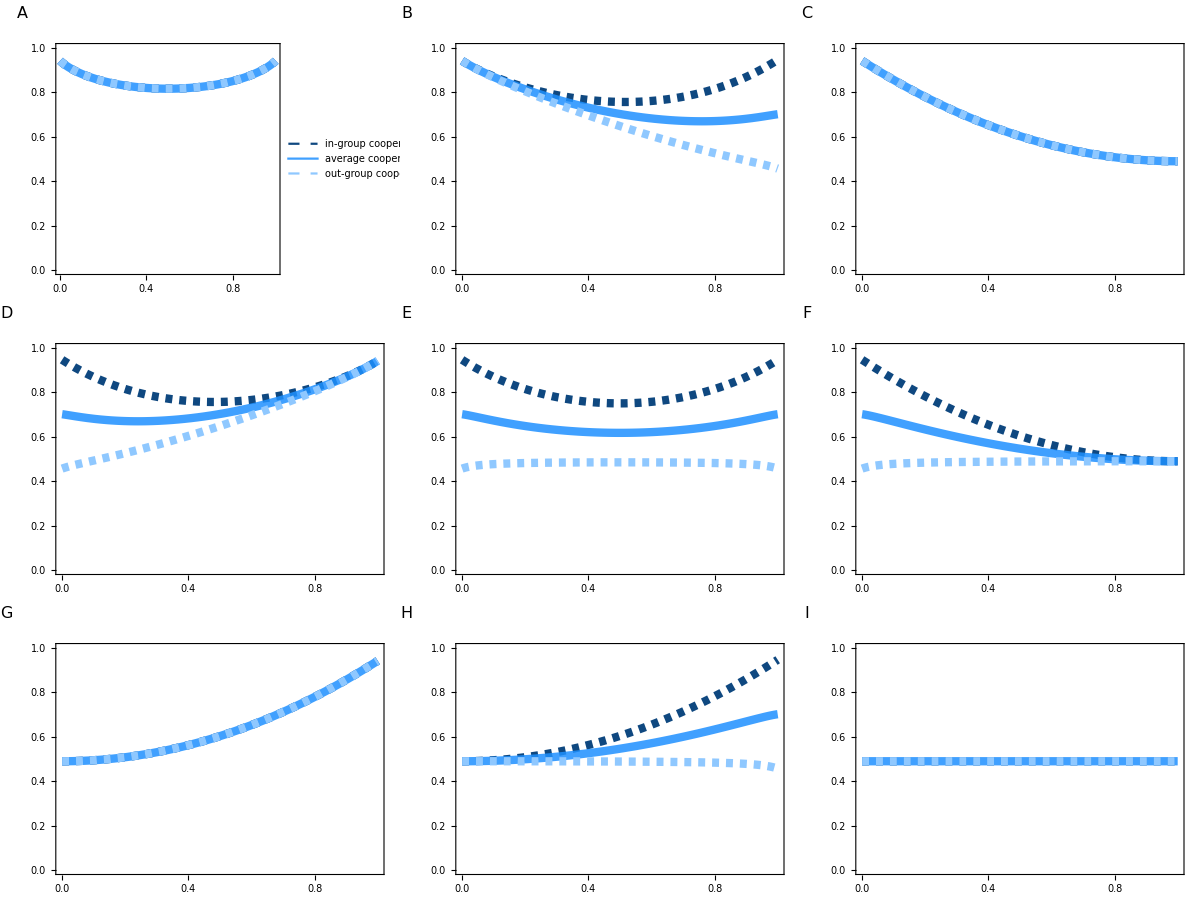
-Graphics-Cooperation level          Stereotype-use propensity (p)

```mathematica
uaval=.02;upval=.02;
coopinoutmonomorphic[uaval,upval]
```

```mathematica
(* Figure 2 with SJ *)
Export[directory<>"Fig2_"<>norm<>".pdf",%];

(* for the other norms (Figures S2-S4), return to section 0 (above) and change the norm under "Set norm", and then run section 1 *)
(*Export[directory<>"FigSG_"<>norm<>".pdf",%];*)
```

## 2. Pairwise invasibility plots (Figure S5)

### Define functions

```mathematica
Clear[invasibilitydata,invasibilitydatafull,invasibilityplot2]
(* compute invasibility condition for select points and interpolate manually in between *)
invasibilitydata[nu_,ua_,up_,a_,b_,c_,Atype_,Btype_,pRstep_,pQstep_]:=Module[{zkeep,invasibility},
zkeep=0;
Flatten[Table[{pR,pQ,
If[AnyTrue[Qvals[pR,pQstep],#==pQ&], (* MemberQ somehow misses some values of pQ *)
(* for the key values of pQ (that are in Qvals[pR,s]), compute the invasibility condition *)
invasibility=(canZQinvadeZR[pQ,pR,ua,up,Atype,Btype,nu,a,b,c]/.nsoln[pQ,pR,ua,up,Atype,Btype,0]);
zkeep=If[invasibility>0,1,-1];
invasibility, (*If[(pQ!=0)&&(pQ!=1),Print[pR,", ",pQ,", ",zkeep]];*)
(* else use the dummy variable *)
zkeep
]},
{pR,0,1,pRstep},{pQ,0,1,pQstep}
],1]
]
(* compute invasibility condition for every point *)
invasibilitydatafull[nu_,ua_,up_,a_,b_,c_,Atype_,Btype_,pRstep_,pQstep_,pRrange_:{0,1},pQrange_:{0,1}]:=Module[{zkeep,invasibility},
Flatten[Table[{pR,pQ,
canZQinvadeZR[pQ,pR,ua,up,Atype,Btype,nu,a,b,c]/.nsoln[pQ,pR,ua,up,Atype,Btype,0]
},
{pR,pRrange[[1]],pRrange[[2]],pRstep},{pQ,pQrange[[1]],pQrange[[2]],pQstep}
],1]
]
(* make invasibility plots *)
(* version that converts tuples into a matrix first *)
invasibilityplot2[data_,Atype_,Btype_,gridtype_:"grid",mode_:"tiger",xlabel_:"Resident (p_R)",ylabel_:"Invader (p_Q)",plotlabel_:Null,pRstep_:Null,pRrange_:{0,1},pQrange_:{0,1},arrows_:{}]:=Module[{dataz,panellabel,PIP},
If[pRstep==Null,
dataz=Transpose[Partition[data[[All,3]],Sqrt@First@Dimensions@data]],
dataz=Transpose[Partition[data[[All,3]],1/pRstep+1]]
];
panellabel=If[gridtype=="grid",3*(2-Atype)+(2-Btype)+1,
If[gridtype=="row",(2-Atype)+4,
If[gridtype=="grid-a",(2-Atype)+3*If[First@StringCases[plotlabel,x:NumberString:>ToExpression[x]]==0.5,1,0]+1]]]; 
PIP=ListDensityPlot[dataz,
PlotRange->All,
DataRange->{pRrange,pQrange},
ColorFunction:>If[mode=="raw",(Blend[{{-.0005,Blue},{0,Gray},{.0005,Red}},#]&),(If[#>0,If[mode=="tiger",Orange,If[mode=="bw",White]],Black]&)],
PlotLegends->If[mode=="raw",Automatic,None],
PlotLabel->If[gridtype=="row",Style[" \n ",10,White](*Style[typelabeldiag[Atype,Btype],10,Black]*),None],
ImageSize->Automatic->{100,100},
ImagePadding->{{If[Btype==0,60,60],If[gridtype=="row",60,60]},{If[Atype==0,60,60],If[gridtype=="row",5,If[Atype==2,70,60]]}},
FrameLabel->If[gridtype=="grid",{{ylabel,Style[Framed[Rotate[typelabelrep[Atype,Btype],-π]],Black]},{xlabel,Style[Framed@typelabelstereo[Atype,Btype],Black]}},
If[gridtype=="row",{{ylabel,None},{xlabel,None}},
If[gridtype=="grid-a",{{ylabel,Style[Framed[Rotate[typelabelstereo[Atype,Btype],-π]],Black]},{xlabel,Style[plotlabel,Black]}}]
]
],
Epilog->Inset[Style[ToUpperCase@FromLetterNumber[panellabel],16],Offset[{0,0},If[gridtype=="row",Scaled[{-0.15,1.15}],Scaled[{-0.13,1.15}]]]]
];
Show[{PIP,arrows}]
]
```

### Pairwise invasion plots -- Full

```mathematica
nuval=0.5;
upval=.02;
uaval=.02;
cval=1.;
bval=3.;
aval=.3;
ppRstep=0.1/4/2;
ppQstep=ppRstep;
mode="bw";
```

```mathematica
Timing[
Grid[
Table[
plotdata=invasibilitydatafull[nuval,uaval,upval,aval,bval,cval,Ai,Bi,ppRstep,ppQstep];
invasibilityplot2[plotdata,Ai,Bi,"grid","bw"],
{Ai,{2,1,0}},{Bi,{2,1,0}}
],
Spacings->{-6.25,-6.25}
]
]//Last
```

$Aborted

```mathematica
(*this figure is large takes a long time to export; save manually instead*)
filename="FigS5.pdf"
```

FigS5.pdf

## 3. Fitness (Figure S7)

### Define functions

```mathematica
Clear[coopcolors,fitnessZQ,fitnessmonomorphic,fitcolors,fitcolors2]

coopcolors = {RGBColor["#0f4880"],RGBColor["#1e90ff"],RGBColor["#8FC8FF"]};
fitcolors={coopcolors[[1]],Blend[{coopcolors[[1]],coopcolors[[2]]},2/3],Blend[{coopcolors[[2]],coopcolors[[3]]},1/3],coopcolors[[3]]};
fitcolors2={coopcolors[[1]],Red,Blend[{coopcolors[[2]],coopcolors[[3]]},1/3],coopcolors[[3]]};(*for demo only*)

fitnessZQ[pQQ_, pRR_,uaa_,upp_,Atype_,Btype_,nu1_,a_,b_,c_]:=Module[{A11,A12,B11,B12,A21,A22,B21,B22,piQ},
A11 = KroneckerDelta[Atype, 1] + KroneckerDelta[Atype, 2];
A12 = KroneckerDelta[Atype, 2];
B11 = KroneckerDelta[Btype, 1] + KroneckerDelta[Btype, 2];
B12 = KroneckerDelta[Btype, 2];
A21 = A12;
A22 = A11;
B21 = B12;
B22 = B11;

piQ={
(1-upp)*(b(nu1 (pIndiv1 g11ZQ+pStype1 g11S)+(1-nu1)(pIndiv1 g12ZQ+pStype1 g12S))-c((1-pQQ)gbul1+pQQ gstar1))-a(1-pQQ),
(1-upp)*(b(nu1 (pIndiv2 g21ZQ+pStype2 g21S)+(1-nu1)(pIndiv2 g22ZQ+pStype2 g22S))-c((1-pQQ)gbul2+pQQ gstar2))-a(1-pQQ)
}/.{pQ->pQQ,pR->pRR};

1/2(piQ[[1]]+piQ[[2]])
]

fitnessmonomorphic[ua_,up_,nu1_,as_,b_,c_,demo_:False]:=
Legended[Labeled[Grid[Table[
Plot[
{
fitnessZQ[rr,rr,ua,up,Ai,Bi,nu1,as[[1]],b,c]/.{fZQ1->0.,fZQ2->0.}/. nsoln[rr,rr,ua,up,Ai, Bi,0],
fitnessZQ[rr,rr,ua,up,Ai,Bi,nu1,as[[2]],b,c]/.{fZQ1->0.,fZQ2->0.}/. nsoln[rr,rr,ua,up,Ai, Bi,0],
fitnessZQ[rr,rr,ua,up,Ai,Bi,nu1,as[[3]],b,c]/.{fZQ1->0.,fZQ2->0.}/. nsoln[rr,rr,ua,up,Ai, Bi,0],
fitnessZQ[rr,rr,ua,up,Ai,Bi,nu1,as[[4]],b,c]/.{fZQ1->0.,fZQ2->0.}/. nsoln[rr,rr,ua,up,Ai, Bi,0]
},
 {rr,0,1},
PlotStyle->If[demo==True,
Evaluate[{fitcolors2[[#]],Thickness[0.01]}&/@Range[Length@as]],
Evaluate[{fitcolors[[#]],Thickness[0.01]}&/@Range[Length@as]]
],
PlotRange->{0.,b/3*2},
PlotRangePadding->0.05,
ImageSize->Automatic->{100,100},
ImagePadding->{{If[Bi==2,25,60],If[Bi==0,80,60]},{If[Ai==0,25,60],If[Ai==2,80,60]}},
FrameLabel->{{None,Style[Framed[Rotate[typelabelrep[Ai,Bi],-π]],Black]},{None,Style[Framed@typelabelstereo[Ai,Bi],Black]}},
FrameTicks->{
({#,Style[NumberForm[#,{20,1}],11],{0,0.02}}&)/@Subdivide[0.,1.,5],
({#,Style[NumberForm[#,{20,1}],11],{0,0.02}}&)/@Subdivide[0.,2.,4]
},
Epilog->Inset[Style[ToUpperCase@FromLetterNumber[3*(2-Ai)+(2-Bi)+1],16],Offset[{0,0},Scaled[{-0.15,1.13}]]]
],
(*{Ai,{1}},{Bi, {1}}*)
{Ai,{2,1,0}},{Bi, {2,1,0}}
],
Spacings->{-6.25,-6.25}
],
{Style["Fitness             ",18,Black],Style["Stereotype-use propensity (p)       ",18,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],
LineLegend[Directive@{fitcolors[[#]]}&/@Range[Length@as],"η = "<>ToString@NumberForm[avals[[#]],{20,1}]&/@Range[Length@as],
LegendLabel->Style["Access cost",12]]
]
```

### Fitness plots

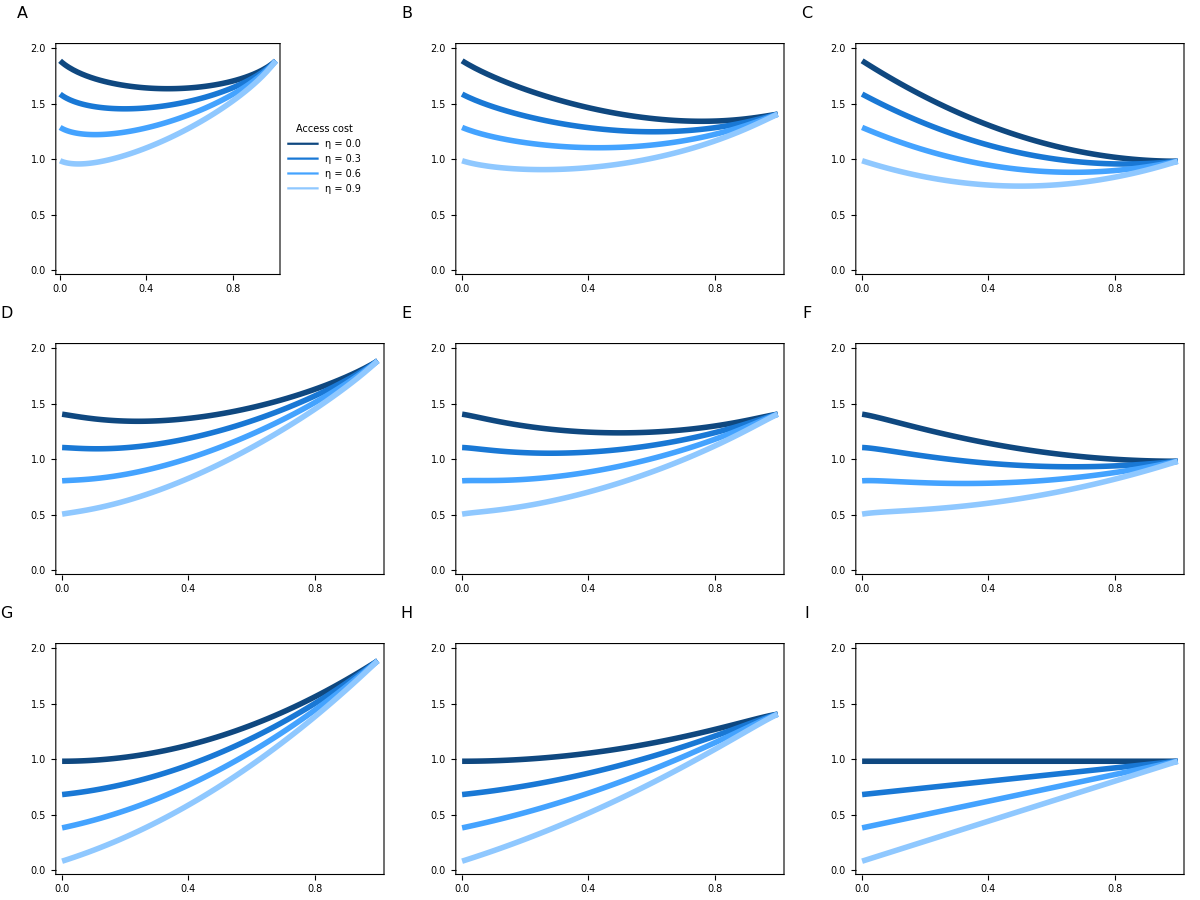
-Graphics-Fitness             Stereotype-use propensity (p)

```mathematica
uaval=.02;upval=.02;nu1=0.5;(*aval=0.1;*)bval=3;cval=1;
avals={0.0,0.3,0.6,0.9};(*avals={0.00,0.15,0.30,0.45,0.60};*)
fitnessmonomorphic[uaval,upval,nu1,avals,bval,cval]
```

```mathematica
Export[directory<>"FigS7.pdf",%];
```

## 4. Dynamic attractors (Figure 3)

### Define functions

```mathematica
(*Clear[flattendata,plotUpDown,listarrows,singularbcsweep,singularasweep,singularupsweep,singularuasweep,singulartablebc,singulartablea,singulartableup,singulartableua];*)
Clear[flattendata,listarrows,singulartablebc,singulartablea,singulartableup,singulartableua];

flattendata[data_]:=Flatten[Table[Table[
Flatten@{data[[i,1]],data[[i,2,j]]},{j,1,Length@data[[i,2]]}],{i,1,Length@data}
],1]

listarrows[data_,xcoords_]:=Module[{arrowlist,subdata},
arrowlist={};
If[Length@data==0,Return[arrowlist]];
Table[
If[Length@First@data==3,
subdata=Cases[data,{xcoord,_,_}],
subdata=Cases[data,{xcoord,_,_,_,_,_,_}]
];
subdata=Sort[subdata];(*Print[subdata];*)

If[subdata[[1,Length@First@data]]=="decrease"&&subdata[[2,Length@First@data]]=="increase",
arrowlist=AppendTo[arrowlist,
{{subdata[[1,1]],Min[subdata[[1,2]]+0.02,subdata[[2,2]]-0.04]},{subdata[[2,1]],Max[subdata[[2,2]]-0.02,subdata[[1,2]]+0.04]}}],(*upward arrow*)
If[subdata[[1,Length@First@data]]=="increase"&&subdata[[2,Length@First@data]]=="decrease",
arrowlist=AppendTo[arrowlist,
{{subdata[[2,1]],Max[subdata[[2,2]]-0.02,subdata[[1,2]]+0.04]},{subdata[[1,1]],Min[subdata[[1,2]]+0.02,subdata[[2,2]]-0.04]}}],    (*downward arrow*)
Print["Check x = ",xcoord,": ",subdata]  
]];
If[Length@subdata>2,If[subdata[[1,Length@First@data]]=="decrease",
arrowlist=AppendTo[arrowlist,
{{subdata[[3,1]]+0,Max[subdata[[3,2]]-0.02,subdata[[2,2]]+0.04]},{subdata[[2,1]]+0,Min[subdata[[2,2]]+0.02,subdata[[3,2]]-0.04]}}],    (*downward arrow*)
arrowlist=AppendTo[arrowlist,
{{subdata[[2,1]]+0,Min[subdata[[2,2]]+0.02,subdata[[3,2]]-0.04]},{subdata[[3,1]]+0,Max[subdata[[3,2]]-0.02,subdata[[2,2]]+0.04]}}] (*upward arrow*)
];];
If[Length@subdata>3,If[subdata[[1,Length@First@data]]=="decrease",
arrowlist=AppendTo[arrowlist,
{{subdata[[3,1]]+0,Min[subdata[[3,2]]+0.02,subdata[[4,2]]-0.04]},{subdata[[4,1]]+0,Max[subdata[[4,2]]-0.02,subdata[[3,2]]+0.04]}}],(*upward arrow*)
arrowlist=AppendTo[arrowlist,
{{subdata[[4,1]]+0,Max[subdata[[4,2]]-0.02,subdata[[3,2]]+0.04]},{subdata[[3,1]]+0,Min[subdata[[3,2]]+0.04,subdata[[4,2]]-0.04]}}]    (*downward arrow*)
];],
{xcoord,xcoords}
];
Return[arrowlist]
]

singulartablebc[nu_,ua_,up_,a_,c_,Atype_,Btype_,pRmin_:0.,pRmax_:1.,pRintervals_:10,bmin_:1.,bmax_:3.,bstep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False]:=Module[{ff,sols,data},
data=Table[
(*ff[pR_]:=canZQinvadeZR[0.,pR,ua,up,Atype,Btype,nu,a,bb,c]/.nsoln[0.,pR,ua,up,Atype,Btype,0];*)
ff[pR_]:=If[Max[pR-tol*offsetparam<0],"CHECK",canZQinvadeZR[pR-tol*offsetparam,pR,ua,up,Atype,Btype,nu,a,bb,c]/.nsoln[pR-tol*offsetparam,pR,ua,up,Atype,Btype,0]];
sols=findsingularpoints[ff,pRmin,pRmax,pRintervals,tol,iter,stepbystep];
{bb/c,sols},{bb,bmin,bmax,bstep}
];
data=flattendata[data]
]
singulartablea[nu_,ua_,up_,b_,c_,Atype_,Btype_,pRmin_:0.,pRmax_:1.,pRintervals_:10,amin_:0.,amax_:1.,astep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False]:=Module[{ff,sols,data},
data=Table[
(*ff[pR_]:=canZQinvadeZR[0.,pR,ua,up,Atype,Btype,nu,aa,b,c]/.nsoln[0.,pR,ua,up,Atype,Btype,0];*)
ff[pR_]:=If[Max[pR-tol*offsetparam<0],"CHECK",canZQinvadeZR[pR-tol*offsetparam,pR,ua,up,Atype,Btype,nu,aa,b,c]/.nsoln[pR-tol*offsetparam,pR,ua,up,Atype,Btype,0]];
sols=findsingularpoints[ff,pRmin,pRmax,pRintervals,tol,iter,stepbystep];
{aa/c,sols},{aa,amin,amax,astep}
];
data=flattendata[data]
]
singulartableup[nu_,ua_,a_,b_,c_,Atype_,Btype_,pRmin_:0.,pRmax_:1.,pRintervals_:10,upmin_:0.,upmax_:1.,upstep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False]:=Module[{ff,sols,data},
data=Table[
(*ff[pR_]:=canZQinvadeZR[0.,pR,ua,upp,Atype,Btype,nu,a,b,c]/.nsoln[0.,pR,ua,upp,Atype,Btype,0];*)
ff[pR_]:=If[Max[pR-tol*offsetparam<0],"CHECK",canZQinvadeZR[pR-tol*offsetparam,pR,ua,upp,Atype,Btype,nu,a,b,c]/.nsoln[pR-tol*offsetparam,pR,ua,upp,Atype,Btype,0]];
sols=findsingularpoints[ff,pRmin,pRmax,pRintervals,tol,iter,stepbystep];
{upp,sols},{upp,upmin,upmax,upstep}
];
data=flattendata[data]
]
singulartableua[nu_,up_,a_,b_,c_,Atype_,Btype_,pRmin_:0.,pRmax_:1.,pRintervals_:10,uamin_:0.,uamax_:1.,uastep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False]:=Module[{ff,sols,data},
data=Table[
(*ff[pR_]:=canZQinvadeZR[0.,pR,uaa,up,Atype,Btype,nu,a,b,c]/.nsoln[0.,pR,uaa,up,Atype,Btype,0];*)
ff[pR_]:=If[Max[pR-tol*offsetparam<0],"CHECK",canZQinvadeZR[pR-tol*offsetparam,pR,uaa,up,Atype,Btype,nu,a,b,c]/.nsoln[pR-tol*offsetparam,pR,uaa,up,Atype,Btype,0]];
sols=findsingularpoints[ff,pRmin,pRmax,pRintervals,tol,iter,stepbystep];
{uaa,sols},{uaa,uamin,uamax,uastep}
];
data=flattendata[data]
]
```

```mathematica
Clear[plotUpDownwithcoop,coopinoutlegend,computecoopdata,computecoopdataua,computecoopdataup,colorsBif];

(*custom color function*)
colorsBif[xx_]:=Blend[({#[[1]],RGBColor[#[[2]]]}&)/@{(*{0.5,"#fde725"},*){0.5,"#7ad151"},{0.625,"#22a884"},{0.75,"#2a788e"},{0.875,"#414487"},{1.0,"#440154"}},xx];

coopinoutlegend[colors_]:=
If[norm=="SJ"||norm=="SS",
Column@{BarLegend[{colorsBif,{0.5,1.}},
LegendLabel->Style["Average\ncooperation",10,LineSpacing->{0.6,0}],
LegendMarkerSize->{15,120},
Ticks->Flatten[{({#,Style[#,10,Black]}&)/@Range[0.4,1,0.1]},1]
],
PointLegend[{Gray,Gray,Gray,Gray,Gray},
(Style[#,10]&)/@Reverse@Range[0,0.5,0.25],
LegendMarkerSize->(4*#+3&)/@Reverse@Range[0,0.5,0.25],
LegendMarkers->Graphics[{EdgeForm[{Thickness[Tiny],Gray}],Gray,Disk[]}],
LegendLabel->Style["coop_in-coop_out",10]
]
}
]

(*compute cooperation level based on singular values of p, when sweeping a or b/c; in this case, datapoint[[1]] corresponds to a or b/c*)
computecoopdata[data_,ua_,up_,Atype_,Btype_]:=Module[{incoop,outcoop,avgcoop,diffcoop},
Table[
incoop=coop11[datapoint[[2]],up] /.{fZQ1->0.,fZQ2->0.}/. nsoln[datapoint[[2]],datapoint[[2]],ua,up,Atype,Btype,0];
outcoop=coop12[datapoint[[2]],up]/.{fZQ1->0.,fZQ2->0.} /. nsoln[datapoint[[2]],datapoint[[2]],ua,up,Atype,Btype,0];
avgcoop=coopavg[datapoint[[2]],up] /.{fZQ1->0.,fZQ2->0.}/. nsoln[datapoint[[2]],datapoint[[2]],ua,up,Atype,Btype,0];
diffcoop=incoop-outcoop;
{datapoint[[1]],datapoint[[2]],incoop,outcoop,avgcoop,diffcoop,datapoint[[3]]},
{datapoint,Cases[data,{_,_,_}]}
]
]
(*compute cooperation level based on singular values of p, when sweeping ua; in this case, datapoint[[1]] corresponds to ua*)
computecoopdataua[data_,up_,Atype_,Btype_]:=Module[{incoop,outcoop,avgcoop,diffcoop},
Table[
incoop=coop11[datapoint[[2]],up] /.{fZQ1->0.,fZQ2->0.}/. nsoln[datapoint[[2]],datapoint[[2]],datapoint[[1]],up,Atype,Btype,0];
outcoop=coop12[datapoint[[2]],up] /.{fZQ1->0.,fZQ2->0.}/. nsoln[datapoint[[2]],datapoint[[2]],datapoint[[1]],up,Atype,Btype,0];
avgcoop=coopavg[datapoint[[2]],up] /.{fZQ1->0.,fZQ2->0.}/. nsoln[datapoint[[2]],datapoint[[2]],datapoint[[1]],up,Atype,Btype,0];
diffcoop=incoop-outcoop;
{datapoint[[1]],datapoint[[2]],incoop,outcoop,avgcoop,diffcoop,datapoint[[3]]},
{datapoint,Cases[data,{_,_,_}]}
]
]
(*compute cooperation level based on singular values of p, when sweeping ua; in this case, datapoint[[1]] corresponds to up*)
computecoopdataup[data_,ua_,Atype_,Btype_]:=Module[{incoop,outcoop,avgcoop,diffcoop},
Table[
incoop=coop11[datapoint[[2]],datapoint[[1]]] /.{fZQ1->0.,fZQ2->0.}/. nsoln[datapoint[[2]],datapoint[[2]],ua,datapoint[[1]],Atype,Btype,0];
outcoop=coop12[datapoint[[2]],datapoint[[1]]] /.{fZQ1->0.,fZQ2->0.}/. nsoln[datapoint[[2]],datapoint[[2]],ua,datapoint[[1]],Atype,Btype,0];
avgcoop=coopavg[datapoint[[2]],datapoint[[1]]] /.{fZQ1->0.,fZQ2->0.}/. nsoln[datapoint[[2]],datapoint[[2]],ua,datapoint[[1]],Atype,Btype,0];
diffcoop=incoop-outcoop;
{datapoint[[1]],datapoint[[2]],incoop,outcoop,avgcoop,diffcoop,datapoint[[3]]},
{datapoint,Cases[data,{_,_,_}]}
]
]
```

```mathematica
Clear[plotUpDownwithcoop2,singularbcwithcoop2,singularawithcoop2,singularupwithcoop2,singularuawithcoop2];

plotUpDownwithcoop2[coopdata_,xmin_,xmax_,ymin_,ymax_,Atype_,Btype_,arrowed_:False]:=Module[{dataUp,dataDown,pUp,pDown,arrows,arrowlist},
(*divide data and plot*)
dataUp=Cases[coopdata,{_,_,_,_,_,_,"increase"}][[;;,1;;6]];
dataDown=Cases[coopdata,{_,_,_,_,_,_,"decrease"}][[;;,1;;6]];
pUp=ListPlot[{#}&/@dataUp[[;;,{1,2}]],
PlotMarkers->({Graphics[{colorsBif@#[[1]],Disk[]}],4*#[[2]]+3}&)/@ dataUp[[;;,{5,6}]] ];
pDown=ListPlot[{#}&/@dataDown[[;;,{1,2}]],
PlotMarkers->({Graphics[{colorsBif@#[[1]],Thickness[Small],Circle[]}],4*#[[2]]+3}&)/@ dataDown[[;;,{5,6}]]];
arrows=If[arrowed===True,
arrowlist=listarrows[coopdata,Range[xmin,xmax,(xmax-Round[xmin,0.5])/20][[{3,7,11,15,19}]]];
Graphics[{Thickness[Tiny],Arrowheads[Small],Gray,Arrow[arrowlist]}],
Graphics[](*empty*)
];
Show[{pUp,pDown,arrows},
PlotRange->{{Round[xmin,0.5],xmax},{0,1}},
PlotRangePadding->{0.05*(xmax-Round[xmin,0.5]),0.05},
FrameTicks->{
{({#,Style[PaddedForm[#,{1,1}],10,Black],{0,0.02}}&)/@Subdivide[0.,1.,5],
({#,Style[PaddedForm[#,{1,1}],6,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]},
{({#,Style[PaddedForm[#,{1,1}],10,Black],{0,0.02}}&)/@If[xmax==3||xmax==0.2||xmax==5,Subdivide[Round[xmin,0.5],xmax,4],Subdivide[Round[xmin,0.5],xmax,5]],
({#,Style[PaddedForm[#,{1,1}],12,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]}
},
ImageSize->Automatic->{100,100},
ImagePadding->{{If[Btype==2,25,60],60},{If[Atype==0,25,60],If[Atype==2,70,60]}},
FrameLabel->{{None,Style[Framed[Rotate[typelabelrep[Atype,Btype],-π]],Black]},{None,Style[Framed@typelabelstereo[Atype,Btype],Black]}},
Epilog->Inset[Style[ToUpperCase@FromLetterNumber[3*(2-Atype)+(2-Btype)+1],16],Offset[{0,0},Scaled[{-0.13,1.13}]]]
]
]

singularbcwithcoop2[nu_,ua_,up_,a_,c_,pRmin_:0.,pRmax_:1.,pRintervals_:10,bmin_:1.,bmax_:3.,bstep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False,arrowed_:False]:=Module[{data,coopdata,dataUp,dataDown,pUp,pDown,colors},
Legended[
Labeled[
Grid[
Table[
(*compute data points*)
data=singulartablebc[nu,ua,up,a,c,Ai,Bi,pRmin,pRmax,pRintervals,bmin,bmax,bstep,tol,iter,stepbystep];
coopdata=computecoopdata[data,ua,up,Ai,Bi];
(*plot data points with/without arrows*)
plotUpDownwithcoop2[coopdata,bmin,bmax,pRmin,pRmax,Ai,Bi,arrowed],
{Ai,{2,1,0}},{Bi, {2,1,0}}
],
Spacings->{-6.35,-6.35}
],
{Style["Stereotype-use propensity (p)       ",16,Black],Style["Benefit of cooperation (b)       ",16,Black]},{Left,Bottom},
RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],coopinoutlegend[colors]]]

singularawithcoop2[nu_,ua_,up_,b_,c_,pRmin_:0.,pRmax_:1.,pRintervals_:10,amin_:0.,amax_:1.,astep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False,arrowed_:False]:=Module[{data,coopdata,dataUp,dataDown,pUp,pDown,colors},
Legended[Labeled[Grid[Table[
data=singulartablea[nu,ua,up,b,c,Ai,Bi,pRmin,pRmax,pRintervals,amin,amax,astep,tol,iter,stepbystep];
coopdata=computecoopdata[data,ua,up,Ai,Bi];
plotUpDownwithcoop2[coopdata,amin,amax,pRmin,pRmax,Ai,Bi,arrowed],
{Ai,{2,1,0}},{Bi, {2,1,0}}
],Spacings->{-6.35,-6.35}],
{Style["Stereotype-use propensity (p)       ",16,Black],Style["Access cost for individual reputations (η)       ",16,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],coopinoutlegend[colors]]]

singularuawithcoop2[nu_,up_,a_,b_,c_,pRmin_:0.,pRmax_:1.,pRintervals_:10,uamin_:0.,uamax_:1.,uastep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False,arrowed_:False]:=Module[{data,coopdata,dataUp,dataDown,pUp,pDown,colors},
Legended[Labeled[Grid[Table[
data=singulartableua[nu,up,a,b,c,Ai,Bi,pRmin,pRmax,pRintervals,uamin,uamax,uastep,tol,iter,stepbystep];
coopdata=computecoopdataua[data,up,Ai,Bi];
plotUpDownwithcoop2[coopdata,uamin,uamax,pRmin,pRmax,Ai,Bi,arrowed],
{Ai,{2,1,0}},{Bi, {2,1,0}}
],Spacings->{-6.35,-6.35}],
{Style["Stereotype-use propensity (p)       ",16,Black],Style["Assessment error rate (u_a)       ",16,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],coopinoutlegend[colors]]]

singularupwithcoop2[nu_,ua_,a_,b_,c_,pRmin_:0.,pRmax_:1.,pRintervals_:10,uamin_:0.,uamax_:1.,uastep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False,arrowed_:False]:=Module[{data,coopdata,dataUp,dataDown,pUp,pDown,colors},
Legended[Labeled[Grid[Table[
data=singulartableup[nu,ua,a,b,c,Ai,Bi,pRmin,pRmax,pRintervals,uamin,uamax,uastep,tol,iter,stepbystep];
coopdata=computecoopdataup[data,ua,Ai,Bi];
plotUpDownwithcoop2[coopdata,uamin,uamax,pRmin,pRmax,Ai,Bi,arrowed],
{Ai,{2,1,0}},{Bi, {2,1,0}}
],Spacings->{-6.35,-6.35}],
{Style["Stereotype-use propensity (p)       ",16,Black],Style["Execution error rate (u_e)       ",16,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],coopinoutlegend[colors]]]
```

### Vary access cost

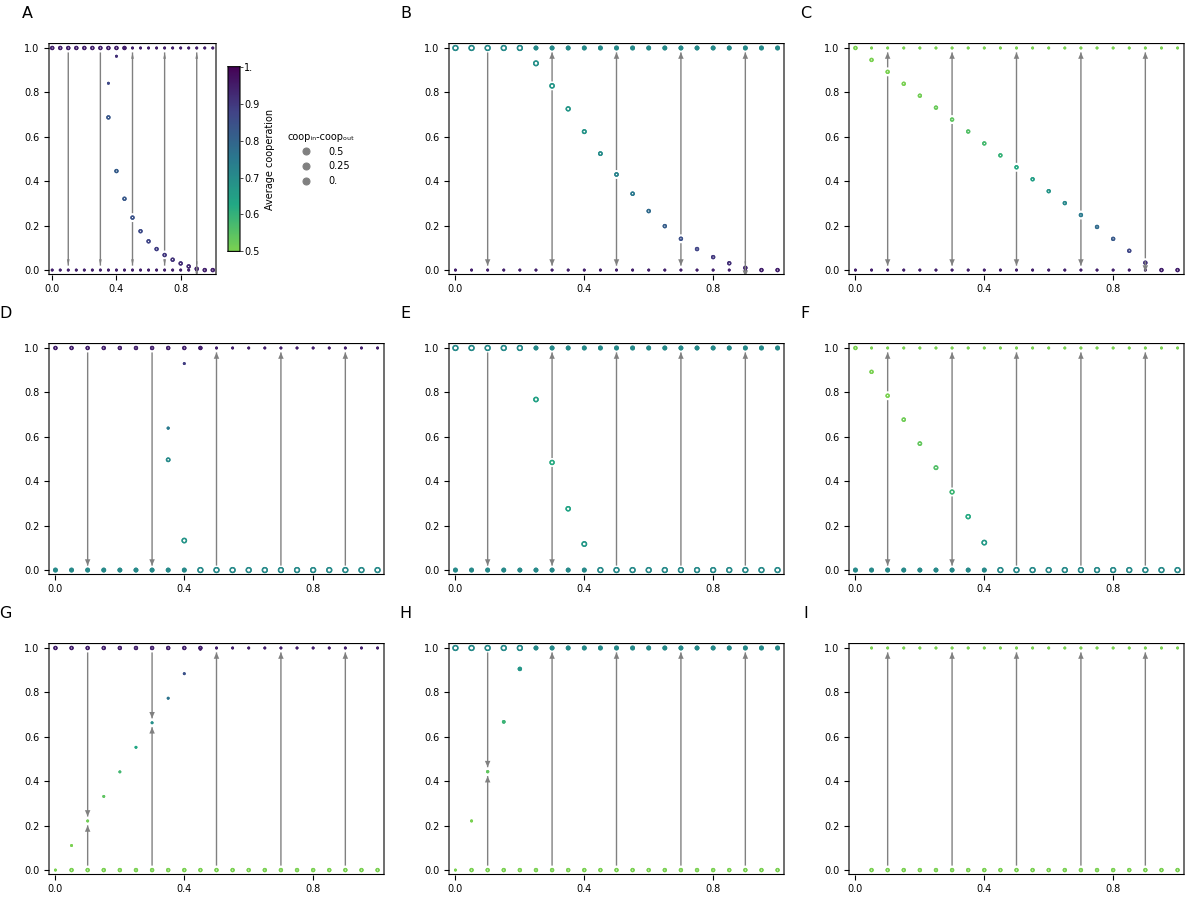
-Graphics-Stereotype-use propensity (p)       Access cost for individual reputations (η)

```mathematica
nuval=0.5;upval=.02;uaval=.02;
(*aval=.2;*)cval=1.;bval=3;
ppRmin=0.;ppRmax=1.;ppRintervals=10;
aamin=0.0;aamax=1.;aastep=0.05;
ttol=10^-10;iiter=100;sstepbystep=False;aarrowed=True;

singularawithcoop2[nuval,uaval,upval,bval,cval,ppRmin,ppRmax,ppRintervals,aamin,aamax,aastep,ttol,iiter,sstepbystep,aarrowed]
```

```mathematica
Export[directory<>"Fig3_"<>norm<>".pdf",%];
```

## 5. Summary plots for dynamic attractors (Figures S8 and S9)

### Define functions

```mathematica
Clear[flattendata2,singulartableabcUp,singulartableuaupUp,countESS3];
Clear[colorsESS,data,heatmaplegend];

flattendata2[data_]:=Flatten[Table[
Flatten@{data[[i,j,1]],data[[i,j,2]],data[[i,j,3,k]]},{i,1,Length@data},{j,1,Length@data[[i]]},{k,1,Length@data[[i,j,3]]}
],2]

singulartableabcUp[nu_,ua_,up_,c_,Atype_,Btype_,pRmin_:0.,pRmax_:1.,pRintervals_:10,amin_:0.,amax_:1.,astep_:0.025,bmin_:1.,bmax_:3.,bstep_:0.1,tol_:10^-10,iter_:100,stepbystep_:False]:=Module[{ff,sols,data},
data=Table[
(*ff[pR_]:=canZQinvadeZR[0.,pR,ua,up,Atype,Btype,nu,aa,bb,c]/.nsoln[0.,pR,ua,up,Atype,Btype,0];*)
ff[pR_]:=If[Max[pR-tol*offsetparam<0],Print@"CHECK",canZQinvadeZR[pR-tol*offsetparam,pR,ua,up,Atype,Btype,nu,aa,bb,c]/.nsoln[pR-tol*offsetparam,pR,ua,up,Atype,Btype,0]];
sols=findsingularpoints[ff,pRmin,pRmax,pRintervals,tol,iter,stepbystep];
{aa,bb/c,sols},
{aa,amin,amax,astep},{bb,bmin,bmax,bstep}
];
data=DeleteDuplicates[flattendata2[data]]
]

singulartableuaupUp[nu_,a_,b_,c_,Atype_,Btype_,pRmin_:0.,pRmax_:1.,pRintervals_:10,uamin_:0.,uamax_:1.,uastep_:0.025,upmin_:1.,upmax_:3.,upstep_:0.1,tol_:10^-10,iter_:100,stepbystep_:False]:=Module[{ff,sols,data},
data=Table[
(*ff[pR_]:=canZQinvadeZR[0.,pR,uaa,upp,Atype,Btype,nu,a,b,c]/.nsoln[0.,pR,uaa,upp,Atype,Btype,0];*)
ff[pR_]:=If[Max[pR-tol*offsetparam<0],Print@"CHECK",canZQinvadeZR[pR-tol*offsetparam,pR,uaa,upp,Atype,Btype,nu,a,b,c]/.nsoln[pR-tol*offsetparam,pR,uaa,upp,Atype,Btype,0]];
sols=findsingularpoints[ff,pRmin,pRmax,pRintervals,tol,iter,stepbystep];
{uaa,upp,sols},
{uaa,uamin,uamax,uastep},{upp,upmin,upmax,upstep}
];
data=DeleteDuplicates[flattendata2[data]]
]

(* countESS3 counts the attractive stable points and categorizes them as follows:,
	1: "p^*= 0 (only)",
	2: "p^*= 0 and 0 < p^*< 1 (bistable)",
	3: "p^*= 0 and p^*= 1 (bistable)",
	4: "0 < p^*< 1 (only)",
	5: "p^*= 1 (only)",
	6: "no ESS",
	7: "more than two ESS" (not seen)
*)
countESS3[data_,xmin_,xmax_,xstep_,ymin_,ymax_,ystep_]:=Module[{regimelist,subdata,datalength,regime,errormessage},
regimelist={};
Table[
regime=Null; (*Reset regime every time*)
datalength=Length@First@data;
subdata=Cases[data,{xcoord,ycoord,_,_}];(*Print[subdata];*)
subdata=Sort[subdata];(*Print[subdata];*)
errormessage[x_,y_,sub_]:=(Print["Check x = ",x,", y = ",y,": ",sub])(*something is wrong**);

If[Length@subdata==0, regime=6];(*There is 0 attractive point*)
If[Length@subdata==2, (*There is 1 attractive ]point*)
If[subdata[[1,datalength]]=="increase" && subdata[[2,datalength]]=="decrease",
If[subdata[[1,3]]==0,regime=1,Print["2"];errormessage[xcoord,ycoord,subdata]],(*p*=0*) 
If[subdata[[1,datalength]]=="decrease" && subdata[[2,datalength]]=="increase",
If[subdata[[2,3]]==1,regime=5,errormessage[xcoord,ycoord,subdata]],(*p*=1*)
If[subdata[[1,datalength]]=="increase" && subdata[[2,datalength]]=="increase"&&subdata[[1,3]]==0&&subdata[[2,3]]==1,
(*this can happen when one of the p*'s is on the cusp of losing stability. this function assigns regime 3 (*p*=0 and p*=1*) in this case but also raises a flag; these coordinates should be manually checked (eg using the pairwise invasibility plots in section 1)*)
Print["Check x = ",xcoord,", y = ",ycoord,"; two 'increase' detected: ",subdata];regime=3,(*p*=0 and p*=1*)
errormessage[xcoord,ycoord,subdata]
]]]];
If[Length@subdata==3,(*1 or 2 attractive points*)
If[subdata[[1,datalength]]=="increase" && subdata[[2,datalength]]=="decrease"&&subdata[[3,datalength]]=="increase",
If[subdata[[1,3]]==0&&subdata[[3,3]]==1,regime=3,(*p*=0 and p*=1*) errormessage[xcoord,ycoord,subdata]],
If[subdata[[1,datalength]]=="decrease" && subdata[[2,datalength]]=="increase"&&subdata[[3,datalength]]=="decrease",
If[subdata[[2,3]]<1&&subdata[[2,3]]>0,regime=4,(*p*=intermediate*) errormessage[xcoord,ycoord,subdata]],
If[subdata[[1,datalength]]=="increase" && subdata[[2,datalength]]=="decrease"&&subdata[[3,datalength]]=="decrease"&&subdata[[1,3]]==0&&(subdata[[2,3]]>0&&subdata[[2,3]]<1)&&subdata[[3,3]]==1,
(*this can happen when a and b are both small and the invasion fitness at y=0.99 is very very close to zero;  this function assigns regime 1 (*p*=0*) in this case but also raises a flag; these coordinates should be manually checked*)
Print["Check x = ",xcoord,", y = ",ycoord,"; 'decrease' detected at y = intermediate: ",subdata];regime=1,(*p*=0 only*)
errormessage[xcoord,ycoord,subdata]
]]]];
If[Length@subdata==4,(*2 attractive points*)
If[subdata[[1,datalength]]=="increase"&& subdata[[2,datalength]]=="decrease"&&subdata[[3,datalength]]=="increase"&&subdata[[4,datalength]]=="decrease",
If[subdata[[1,3]]==0&&subdata[[3,3]]<1,regime=2,(*p*=0 and p*<1*) errormessage[xcoord,ycoord,subdata]], 
If[subdata[[1,datalength]]=="decrease" && subdata[[2,datalength]]=="increase"&&subdata[[3,datalength]]=="decrease"&&subdata[[4,datalength]]=="increase",
errormessage[xcoord,ycoord,subdata] (*we haven't seen this case, but just in case*),
errormessage[xcoord,ycoord,subdata] 
]]];
If[Length@subdata>4,regime=7]; (*there are more than two ESSs*)
regimelist=AppendTo[regimelist,{xcoord,ycoord,regime}],
{xcoord,xmin,xmax,xstep},{ycoord,ymin,ymax,ystep}
];
Return[regimelist]
]

(*custom color function*)
colorsESS[xx_]:=Blend[({#[[1]],RGBColor[#[[2]]]}&)/@{{1,"#c6c6c6"},{2,"#d9936b"},{3,"#d55e00"},{4,"#7f9bbd"},{5,"#0072b2"},{6,"#777777"},{7,Black}},xx]; (*220328*)
colorsESS[xx_]:=Blend[({#[[1]],RGBColor[#[[2]]]}&)/@{{1,"#c6c6c6"},{2,"#8AB0CF"},{3,"#416F9E"},{4,"#A98189"},{5,"#664148"},{6,"#777777"},{7,Black}},xx]; (*220407*)
colorsESS[xx_]:=Blend[({#[[1]],RGBColor[#[[2]]]}&)/@{{1,"#c6c6c6"},{2,"#c79b7f"},{3,"#9B5D32"},{4,"#a18898"},{5,"#66415a"},{6,"#777777"},{7,Black}},xx]; (*220416*)
colorsESS[xx_]:=Blend[({#[[1]],RGBColor[#[[2]]]}&)/@{{1,"#c6c6c6"},{2,"#e0a580"},{3,"#bf6c30"},{4,"#b38aa4"},{5,"#704863"},{6,"#777777"},{7,Black}},xx]; (*220416*)

heatmaplegend:=SwatchLegend[Array[colorsESS,6],
{"p = 0 only","p = 0 only or intermediate p^* (bistable)","p = 0 only or p = 1 only (bistable)","intermediate p^* ","p = 1 only","neutrality"},
LabelStyle->{FontSize->11}
]
```

### Vary cooperation benefit (b) and access cost (a)

```mathematica
(*AAA=2;BBB=2;*)
nuval=0.5;upval=.02;uaval=.02;
(*aval=.3;*)cval=1.;(*bval=2;*)
ppRmin=0.;ppRmax=1.;ppRintervals=10;
aamin=0.;aamax=1.;aastep=.04(*.0125*);
bbmin=1.;bbmax=5.;bbstep=.20(*.025*);
ttol=10^-10;iiter=100;sstepbystep=False;(*aarrowed=True;*)
```

Atype = 2, Btype = 2

Atype = 2, Btype = 1

Atype = 2, Btype = 0

Check x = 0., y = 1.; 'decrease' detected at y = intermediate: {{0.,1.,0.,increase},{0.,1.,0.99,decrease},{0.,1.,1.,decrease}}

Atype = 1, Btype = 2

Atype = 1, Btype = 1

Atype = 1, Btype = 0

Check x = 0., y = 1.; 'decrease' detected at y = intermediate: {{0.,1.,0.,increase},{0.,1.,0.99,decrease},{0.,1.,1.,decrease}}

Atype = 0, Btype = 2

Atype = 0, Btype = 1

Atype = 0, Btype = 0

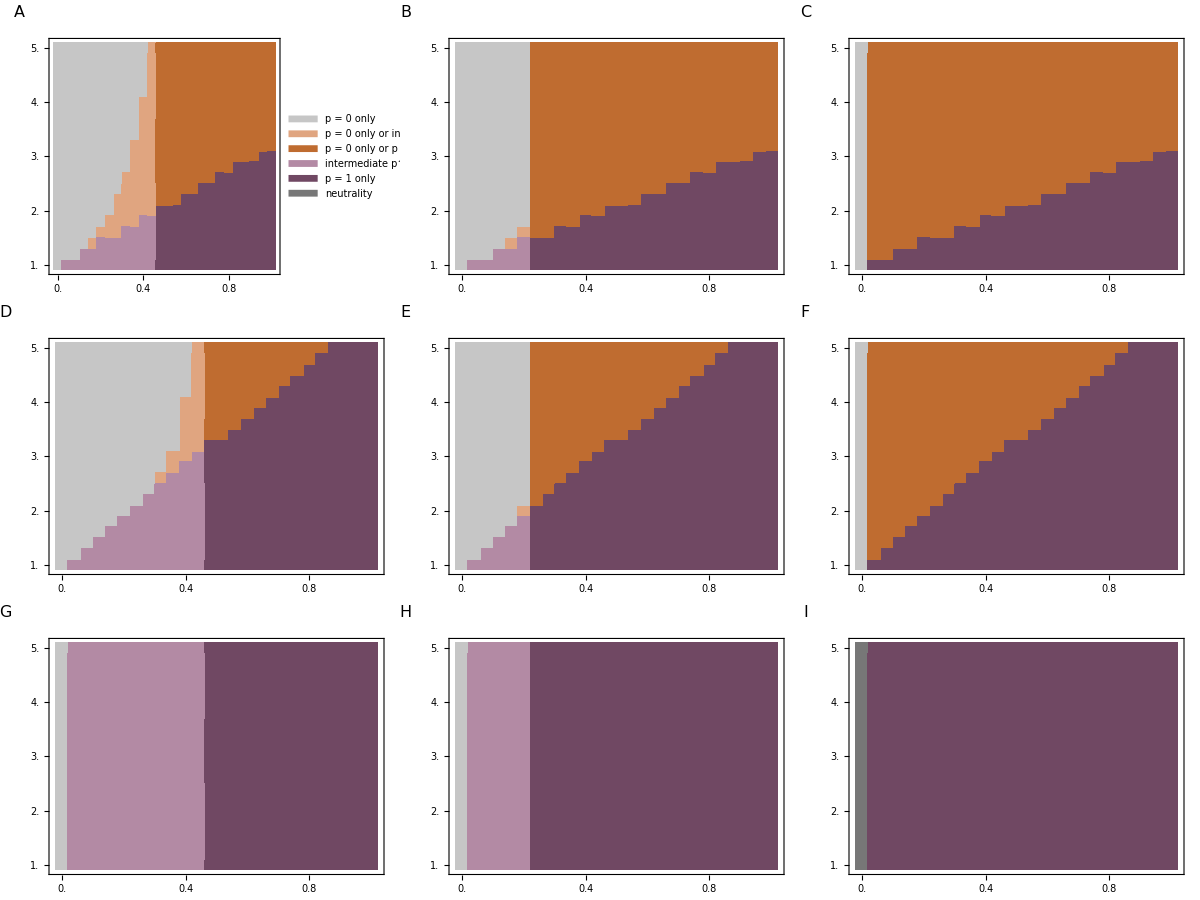
-Graphics-Benefit of cooperation (b)       Access cost for individual reputations (η)

```mathematica
Clear[data,dataESS];

Legended[
Labeled[
Grid[Table[
Print["Atype = ",Ai,", Btype = ",Bi];
data=singulartableabcUp[nuval,uaval,upval,cval,Ai,Bi,ppRmin,ppRmax,ppRintervals,aamin,aamax,aastep,bbmin,bbmax,bbstep,ttol,iiter,sstepbystep]//N;
dataESS=countESS3[data,aamin,aamax,aastep,bbmin,bbmax,bbstep];
ListDensityPlot[dataESS,
ColorFunction->colorsESS,
PlotRange->{{0-aastep/2,1+aastep/2},{1-bbstep/2,bbmax+bbstep/2},All},
FrameTicks->{
{({#,Style[#,10,Black],{0,0.02}}&)/@Subdivide[1.,5.,4],
({#,Style[#,6,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]},
{({#,Style[#,10,Black],{0,0.02}}&)/@Subdivide[0.,1.,5],
({#,Style[#,12,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]}
},
(*Frame->True,
FrameStyle->{{Black,White},{Black,White}},*)
(*FrameTicks->{({#,#,{0,0.02}}&)/@Subdivide[0.,1.,5],({#,#,{0,0.02}}&)/@Subdivide[1.,5.,4]},*)
ImageSize->Automatic->{100,100},
ImagePadding->{{If[Bi==2,25,60],60},{If[Ai==0,25,60],If[Ai==2,70,60]}},
FrameLabel->{{None,Style[Framed[Rotate[typelabelrep[Ai,Bi],-π]],Black]},{None,Style[Framed@typelabelstereo[Ai,Bi],Black]}},
Epilog->Inset[Style[ToUpperCase@FromLetterNumber[3*(2-Ai)+(2-Bi)+1],16],Offset[{0,0},Scaled[{-0.13,1.11}]]]
],
{Ai,{2,1,0}},{Bi,{2,1,0}}
],
Spacings->{-6.5,-6.5}
],
{Style["Benefit of cooperation (b)       ",16,Black],Style["Access cost for individual reputations (η)       ",16,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],
heatmaplegend
]
```

```mathematica
(*large file, so save manually rather than exporting using Export*)
filename="FigS8_summary_a_b.pdf"
```

FigS8_summary_a_b.pdf

### Vary error rates (ua and up)

```mathematica
(*AAA=2;BBB=2;*)
nuval=0.5;(*upval=.02;uaval=.02;*)
aval=.3;cval=1.;bval=3;
ppRmin=0.;ppRmax=1.;ppRintervals=10;
uuamin=.012;uuamax=.3;uuastep=.012;
uupmin=.012;uupmax=.3;uupstep=.012;
ttol=10^-10;iiter=100;sstepbystep=False;(*aarrowed=True;*)
```

Atype = 2, Btype = 2

Atype = 2, Btype = 1

Atype = 2, Btype = 0

Atype = 1, Btype = 2

Atype = 1, Btype = 1

Atype = 1, Btype = 0

Atype = 0, Btype = 2

Atype = 0, Btype = 1

Atype = 0, Btype = 0

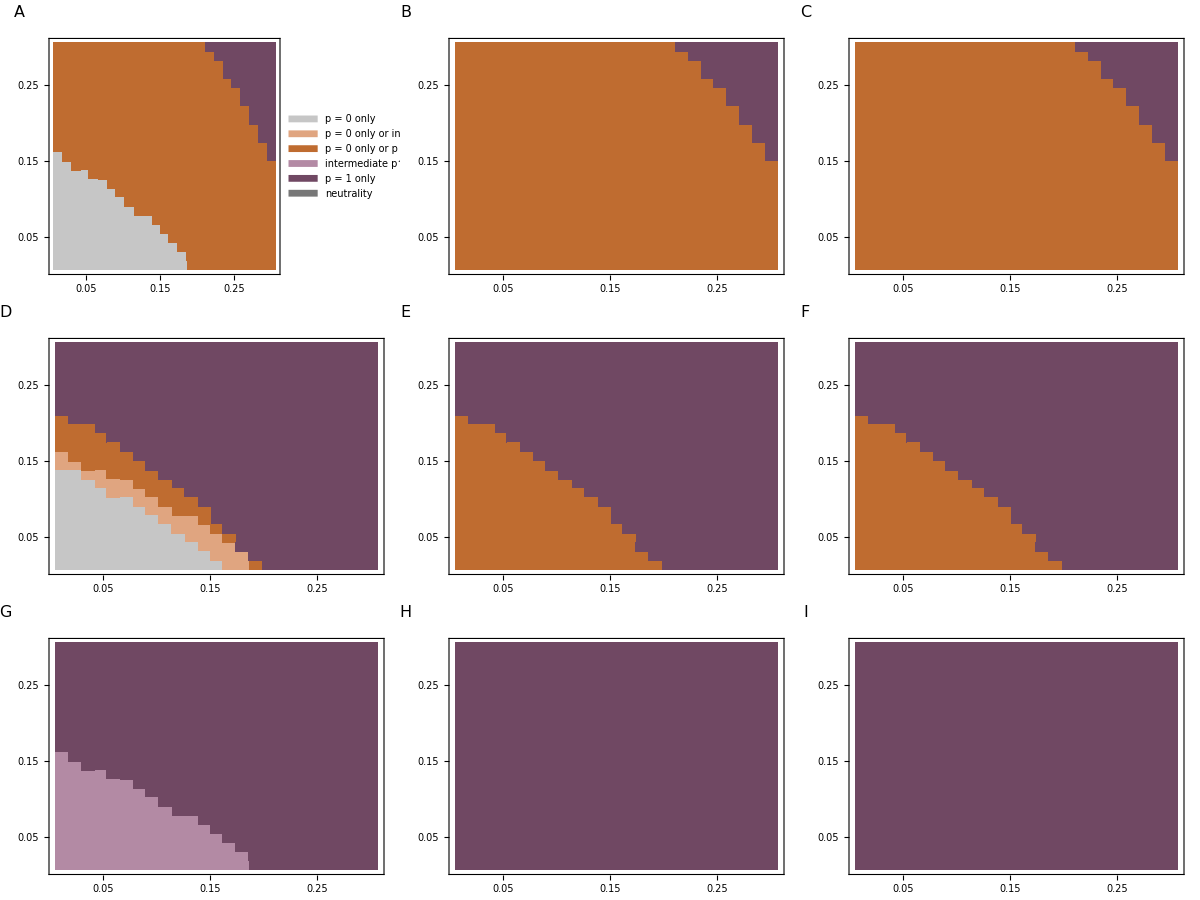
-Graphics-Execution error rate (u_e)    Assessment error rate (u_a)

```mathematica
Legended[
Labeled[
Grid[Table[
Print["Atype = ",Ai,", Btype = ",Bi];
data=singulartableuaupUp[nuval,aval,bval,cval,Ai,Bi,ppRmin,ppRmax,ppRintervals,uuamin,uuamax,uuastep,uupmin,uupmax,uupstep,ttol,iiter,sstepbystep]//N;
dataESS=countESS3[data,uuamin,uuamax,uuastep,uupmin,uupmax,uupstep];
ListDensityPlot[dataESS,
ColorFunction->colorsESS,
PlotRange->{{uuamin-uuastep/2,uuamax+uuastep/2},{uupmin-uupstep/2,uupmax+uupstep/2},All},
FrameTicks->{
{({#,Style[#,10,Black],{0,0.02}}&)/@Subdivide[0.05,uupmax+0.05,Round[uupmax/0.1]],
({#,Style[#,6,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]},
{({#,Style[#,10,Black],{0,0.02}}&)/@Subdivide[0.05,uuamax+0.05,Round[uuamax/0.1]],
({#,Style[#,12,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]}
},
ImageSize->Automatic->{100,100},
ImagePadding->{{If[Bi==2,25,70],60},{If[Ai==0,25,60],If[Ai==2,70,60]}},
FrameLabel->{{None,Style[Framed[Rotate[typelabelrep[Ai,Bi],-π]],Black]},{None,Style[Framed@typelabelstereo[Ai,Bi],Black]}},
Epilog->Inset[Style[ToUpperCase@FromLetterNumber[3*(2-Ai)+(2-Bi)+1],16],Offset[{0,0},Scaled[{-0.13,1.11}]]]
],
{Ai,{2,1,0}},{Bi,{2,1,0}}
],
Spacings->{-7,-6.5}
],
{Style["Execution error rate (u_e)    ",16,Black],Style["Assessment error rate (u_a)    ",16,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],
heatmaplegend
]
```

```mathematica
(*large file, so save manually rather than exporting using Export*)
filename="FigS9_summary_ua_up.pdf"
```

FigS9_summary_ua_up.pdf

## Part 2: Analysis with pDISC and a fixed proportion of ALLD

## 6. Setup for invasibility analysis with general pQ, pR, and ALLD

### Set up functions

```mathematica
Clear["Global`*"];

setupallequations[p_,q_, ua_,up_,nu1_]:=(
(*Clear[ua,up,eps,pgc,pgd,pbc,pbd,nsoln];*)
eps=(1-ua)*(1-up)+ua up;
nu2 = 1.0 - nu1;

A21 = A12;
A22 = A11;
B21 = B12;
B22 = B11;

(* observer view - donor intent - probgood *)
pgc=eps;
pgd=ua;
pbc=p(eps-ua)+q(1-eps-ua)+ua;
pbd=q(1-2ua)+ua;

(* generation equations for reputation relations *)
g11Z=fY1 g11Y+fZQ1 g11ZQ + (1.-fZQ1-fY1) g11ZR;
g12Z=fY1 g12Y+fZQ1 g12ZQ + (1.-fZQ1-fY1) g12ZR;
g21Z=fY2 g21Y+fZQ2 g21ZQ + (1.-fZQ2-fY2)g21ZR;
g22Z=fY2 g22Y+fZQ2 g22ZQ + (1.-fZQ2-fY2) g22ZR;

gbul1 = nu1 g11Z + nu2 g21Z;
gbul2 = nu1 g12Z + nu2 g22Z;
gstar1 = nu1 g11S  + nu2 g21S;
gstar2 = nu1 g12S  + nu2 g22S;

g11a1 = nu1 (fY1 g11Y g11Y+fZQ1 g11ZQ g11ZQ +(1.-fZQ1-fY1) g11ZR g11ZR) + nu2(fY2 g21Y g21Y+fZQ2 g21ZQ g21ZQ +(1.-fZQ2-fY2) g21ZR g21ZR);
g11b1 = gbul1 - g11a1;
g11c1 = gbul1 - g11a1;
g11d1 = 1 - gbul1 - gbul1 + g11a1;
g12a1 = nu1 (fY1 g12Y g11Y+fZQ1 g12ZQ g11ZQ + (1.-fZQ1-fY1) g12ZR g11ZR)+ nu2 (fY2 g22Y g21Y+fZQ2 g22ZQ g21ZQ + (1.-fZQ2-fY2) g22ZR g21ZR);
g12b1 = gbul2 - g12a1;
g12c1 = gbul1 - g12a1;
g12d1 = 1 - gbul2 - gbul1 + g12a1;
g21a1 = nu1(fY1 g11Y g12Y+fZQ1 g11ZQ g12ZQ + (1.-fZQ1-fY1) g11ZR g12ZR)+ nu2 (fY2 g21Y g22Y+fZQ2 g21ZQ g22ZQ + (1.-fZQ2-fY2)g21ZR g22ZR);
g21b1 = gbul1 - g21a1;
g21c1 = gbul2 - g21a1;
g21d1 = 1 - gbul1 - gbul2 + g21a1;
g22a1 = nu1(fY1 g12Y g12Y+fZQ1 g12ZQ g12ZQ +  (1.-fZQ1-fY1) g12ZR g12ZR)+ nu2 (fY2 g22Y g22Y+fZQ2 g22ZQ g22ZQ + (1.-fZQ2-fY2) g22ZR g22ZR);
g22b1 = gbul2 - g22a1;
g22c1 = gbul2 - g22a1;
g22d1 = 1 - gbul2 - gbul2 + g22a1;
g11a2 = nu1 g11S g11Z + nu2 g21S g21Z;
g11b2 = gbul1 - g11a2;
g11c2 = gstar1 - g11a2;
g11d2 = 1 - gbul1 - gstar1 + g11a2;
g12a2 = nu1 g12S g11Z + nu2 g22S g21Z;
g12b2 = gbul2 - g12a2;
g12c2 = gstar1 - g12a2;
g12d2 = 1 - gbul2 - gstar1 + g12a2;
g21a2 = nu1 g11S g12Z + nu2 g21S g22Z;
g21b2 = gbul1 - g21a2;
g21c2 = gstar2 - g21a2;
g21d2 = 1 - gbul1 - gstar2 + g21a2;
g22a2 = nu1 g12S g12Z + nu2 g22S g22Z;
g22b2 = gbul2 - g22a2;
g22c2 = gstar2 - g22a2;
g22d2 = 1 - gbul2 - gstar2 + g22a2;
g11a3 = nu1 g11Z g11S + nu2 g21Z g21S;
g11b3 = gstar1 - g11a3;
g11c3 = gbul1 - g11a3;
g11d3 = 1 - gstar1 - gbul1 + g11a3;
g12a3 = nu1 g12Z g11S + nu2 g22Z g21S;
g12b3 = gstar2 - g12a3;
g12c3 = gbul1 - g12a3;
g12d3 = 1 - gstar2 - gbul1 + g12a3;
g21a3 = nu1 g11Z g12S + nu2 g21Z g22S;
g21b3 = gstar1 - g21a3;
g21c3 = gbul2 - g21a3;
g21d3 = 1 - gstar1 - gbul2 + g21a3;
g22a3 = nu1 g12Z g12S + nu2 g22Z g22S;
g22b3 = gstar2 - g22a3;
g22c3 = gbul2 - g22a3;
g22d3 = 1 - gstar2 - gbul2 + g22a3;
g11a4 = nu1 g11S g11S + nu2 g21S g21S;
g11b4 = gstar1 - g11a4;
g11c4 = gstar1 - g11a4;
g11d4 = 1 - gstar1 - gstar1 + g11a4;
g12a4 = nu1 g12S g11S + nu2 g22S g21S;
g12b4 = gstar2 - g12a4;
g12c4 = gstar1 - g12a4;
g12d4 = 1 - gstar2 - gstar1 + g12a4;
g21a4 = nu1 g11S g12S + nu2 g21S g22S;
g21b4 = gstar1 - g21a4;
g21c4 = gstar2 - g21a4;
g21d4 = 1 - gstar1 - gstar2 + g21a4;
g22a4 = nu1 g12S g12S + nu2 g22S g22S;
g22b4 = gstar2 - g22a4;
g22c4 = gstar2 - g22a4;
g22d4 = 1 - gstar2 - gstar2 + g22a4;

g11Zpriv=g11a1 pgc + g11b1 pgd + g11c1 pbc + g11d1 pbd;
g12Zpriv=g12a1 pgc + g12b1 pgd + g12c1 pbc + g12d1 pbd;
g21Zpriv=g21a1 pgc + g21b1 pgd + g21c1 pbc + g21d1 pbd;
g22Zpriv=g22a1 pgc + g22b1 pgd + g22c1 pbc + g22d1 pbd;
g11Zpub=gbul1 pgc + (1-gbul1)pbd;
g12Zpub=gbul2 pgc + (1-gbul2)pbd;
g21Zpub=gbul1 pgc + (1-gbul1)pbd;
g22Zpub=gbul2 pgc + (1-gbul2)pbd;
g11Zind=g11a2 pgc + g11b2 pgd + g11c2 pbc + g11d2 pbd;
g12Zind=g12a2 pgc + g12b2 pgd + g12c2 pbc + g12d2 pbd;
g21Zind=g21a2 pgc + g21b2 pgd + g21c2 pbc + g21d2 pbd;
g22Zind=g22a2 pgc + g22b2 pgd + g22c2 pbc + g22d2 pbd;
g11SZind=g11a3 pgc + g11b3 pgd + g11c3 pbc + g11d3 pbd;
g12SZind=g12a3 pgc + g12b3 pgd + g12c3 pbc + g12d3 pbd;
g21SZind=g21a3 pgc + g21b3 pgd + g21c3 pbc + g21d3 pbd;
g22SZind=g22a3 pgc + g22b3 pgd + g22c3 pbc + g22d3 pbd;
g11SZpriv=g11a4 pgc + g11b4 pgd + g11c4 pbc + g11d4 pbd;
g12SZpriv=g12a4 pgc + g12b4 pgd + g12c4 pbc + g12d4 pbd;
g21SZpriv=g21a4 pgc + g21b4 pgd + g21c4 pbc + g21d4 pbd;
g22SZpriv=g22a4 pgc + g22b4 pgd + g22c4 pbc + g22d4 pbd;
g11SZpub=gstar1 pgc +(1-gstar1) pbd;
g12SZpub=gstar2 pgc +(1-gstar2) pbd;
g21SZpub=gstar1 pgc +(1-gstar1) pbd;
g22SZpub=gstar2 pgc +(1-gstar2) pbd;

(*probability that individuals in each group uses reputations / stereotypes*)
pIndiv1=fZQ1(1-pQ)+(1-fZQ1-fY1)(1-pR);
pStype1=fZQ1 *pQ+(1-fZQ1-fY1)pR;
pIndiv2=fZQ2(1-pQ)+(1-fZQ2-fY2)(1-pR);
pStype2=fZQ2 *pQ+(1-fZQ2-fY2)pR;

(* general equation to solve for equilibrium reputations; we use FindRoot which is fast but requires initial guess *)

ng11Z := g11Z;
ng12Z := g12Z;
ng21Z := g21Z ;
ng22Z := g22Z ;
ng11S := g11S;
ng12S := g12S;
ng21S := g21S;
ng22S := g22S;

(* cooperation levels *)
coop11[pstar_,fY_,upp_] := (1-upp)*(1-fY)((1-pstar)ng11Z + pstar ng11S);
coop12[pstar_,fY_,upp_] := (1-upp)*(1-fY)((1-pstar) ng21Z + pstar ng21S);
coop21[pstar_,fY_,upp_] := (1-upp)*(1-fY)((1-pstar)ng12Z + pstar ng12S);
coop22[pstar_,fY_,upp_] := (1-upp)*(1-fY)((1-pstar) ng22Z + pstar ng22S);
coopavg[pstar_,fY_,upp_]:=(coop11[pstar,fY,upp]+coop12[pstar,fY,upp])/2
)

(* Manually compute the root using the secant method *)
Clear[secantmethod,edgecheck,findsingularpoints, offset];
secantmethod[f_,x0_,x1_,tol_:10^-10,iter_:50,stepbystep_:False]:=Module[{fx0,fx1,fx2,xx0,xx1,xx2,dir,i},
xx0=x0;
xx1=x1;
fx0=N@Evaluate[f[xx0]];
fx1=N@Evaluate[f[xx1]];
If[stepbystep==True,Print["start from: x0 = ",xx0,", x1 = ",xx1]];
(* check that we haven't found the root yet *)
If[Abs[fx0]<tol&&Abs[fx1]>tol,
If[stepbystep==True,Print["\tYou already found the root at x = ",xx0,", where f(x0) = ",fx0,". f(x0+tol) = ",N@Evaluate[f[xx0+tol]]]];
dir=If[N@Evaluate[f[xx0+tol]]>fx0,"increase","decrease"];
Return[{xx0,dir}]
];
If[Abs[fx1]<tol&&Abs[fx0]>tol,
If[stepbystep==True,Print["\tYou already found the root at x = ",xx1,", where f(x1) = ",fx1,". f(x1-tol) = ",N@Evaluate[f[xx1-tol]]]];
dir=If[N@Evaluate[f[xx1-tol]]<fx1,"increase","decrease"];
Return[{xx1,dir}]
];
(* check that f(x0) and f(x1) have different signs *)
If[fx0*fx1>=0,
If[stepbystep==True,Print["\tNeed f(x0)*f(x1)<0; check x0 and x1 values"]];Return[]];
(* iteratively find root *)
i=0;
While[i<=iter,
(* update guessed root *)
xx2=(xx0*fx1-xx1*fx0)/(fx1-fx0);
fx2=N@Evaluate[f[xx2]];
If[Abs[fx2]<tol,
(* found the root *)
If[stepbystep==True,Print["\tFound root x = ",xx2," after ",i," iterations"]];
dir=If[fx1>fx0,"increase","decrease"];
Return[{xx2,dir}],
(* haven't found the root; update x0 and x1 *)
If[stepbystep==True,Print["\titeration ",i,": f(",xx0,") = ",fx0,", f(",xx1,") = ",fx1]];
If[fx0*fx2>0,xx0=xx2;fx0=fx2,
If[fx1*fx2>0,xx1=xx2;fx1=fx2,Print["!!! check x values !!!: x0 = ",xx0,", x1 = ",xx1,", x2 = ",xx2]]
];
i++
];
]
]

offsetparam=10.^4;

edgecheck[f_,xmin_:0.,xmax_:1.,tol_:10^-10,stepbystep_:False]:=Module[{mindir,maxdir,fxmin,fxmax,fxminδ,fxmaxδ},
(*fxmin=N@Evaluate[f[xmin]];*)(*version for sweeping pQ=0*)
(*fxmax=N@Evaluate[f[xmin]];*)(*version for sweeping pQ=0*)
(*fxminδ=f[xmin+tol];*)(*version for sweeping pQ=0*)
(*fxmaxδ=f[xmax-tol];*)(*version for sweeping pQ=0*)
fxmin=0.;fxmax=0; (*version for sweeping just below*)
fxminδ=f[xmin+offsetparam*tol];
fxmaxδ=f[xmax-offsetparam*tol];

mindir=If[fxmin<fxminδ,"increase","decrease"];
maxdir=If[fxmaxδ<fxmax,"increase","decrease"];
If[stepbystep==True,
(*Print[{{xmin,fxmin,fxminδ},{xmax,fxmaxδ,fxmax}}];*)
Print["At xmin = ",xmin,", f(xmin) = ",fxmin,", whereas f(xmin+tol) = ",fxminδ];
Print["At xmax = ",xmax,", f(xmax) = ",fxmax,", whereas f(xmax-tol) = ",fxmaxδ];
Print[{{xmin,mindir},{xmax,maxdir}}];
];
Return[{{xmin,mindir},{xmax,maxdir}}]
]

findsingularpoints[f_,xmin_:0.,xmax_:1.,xintervals_:10,tol_:10^-10,iter_:50,stepbystep_:False,param_:Null]:=Module[{breaks,sol,sollist,soltable,edgesol},
(*search for intermediate singular points*)
If[stepbystep==True,Print[Information@f]];
sollist={};
breaks=Sort@Flatten@{N@Subdivide[xmin+tol*offsetparam,xmax-tol*offsetparam,xintervals],0.01,0.99}; (*x=0 and 1 are checked by edgecheck*)
(*If[AllTrue[breaks,(Abs[f[#]]<tol&)]&&AllTrue[{0.,1.},(Abs[f[#]]<tol&)],*)(*version for sweeping pQ=0*)
If[AllTrue[breaks,(Abs[f[#]]<tol&)],
(*if f evaluated at all initial points for the secand method and the edge values, raise a flag*)
If[stepbystep==True,Print["f is zero at all break values; likely a neutral case. Check param = ",param]];
sollist={}, (*redundant but making explicit*)
(*otherwise*)
If[stepbystep==True,Print[breaks]];
soltable=Table[
sol=secantmethod[f,breaks[[j]],breaks[[j+1]],tol,iter,stepbystep];
sollist=AppendTo[sollist,sol];
{breaks[[j]],breaks[[j+1]],sol},
{j,1,xintervals+2}
];
If[stepbystep==True,Print[soltable//MatrixForm]];
(*check edge cases*)
edgesol=edgecheck[f,xmin,xmax,tol,stepbystep];
sollist=Last@(AppendTo[sollist,#]&/@edgesol);
(*select unique elements*)
If[stepbystep==True,Print[sollist]];
(*first, check if there are any neighboring intermediate points*)
sollist=DeleteDuplicates[Sort@Cases[Chop[N@sollist,tol*offsetparam],{_?NumericQ,_}],(#1[[2]]==#2[[2]]&&Abs[#1[[1]]-#2[[1]]]<tol*offsetparam)&]; 
(*then check edgees*)
sollist=DeleteDuplicates[sollist,((#1[[1]]==0.||#1[[2]]==0.)&&#1[[2]]==#2[[2]]&&Abs[#1[[1]]-#2[[1]]]<tol*offsetparam*1.01)&]; (*check 0*)
sollist=DeleteDuplicates[Reverse@sollist,((#1[[1]]==1.||#1[[2]]==1.)&&#1[[2]]==#2[[2]]&&Abs[#1[[1]]-#2[[1]]]<tol*offsetparam*1.01)&]; (*check 1*)
];
If[stepbystep==True,Print[sollist]];
Return[sollist]
]
```

### Set norm

```mathematica
Clear[nu];nu=.5;
norm="SJ";setupallequations[0,1, ua,up,nu]
(*norm="SS";setupallequations[1,1, ua,up,nu]*)
(*norm="SC";setupallequations[1,0, ua,up,nu];*)
(*norm="SH";setupallequations[0,0, ua,up,nu];*)
```

### Invasibility conditions

```mathematica
(*full version*)
nsoln[pQQ_,pRR_,uaa_,upp_,Atype_, Btype_,fZQ_,fY_] :=Module[{A11,A12,B11,B12,A21,A22,B21,B22},
A11 = KroneckerDelta[Atype, 1] + KroneckerDelta[Atype, 2];
A12 = KroneckerDelta[Atype, 2];
B11 = KroneckerDelta[Btype, 1] + KroneckerDelta[Btype, 2];
B12 = KroneckerDelta[Btype, 2];
A21 = A12;
A22 = A11;
B21 = B12;
B22 = B11;

FindRoot[{
g11Y==gbul1 pgd+(1-gbul1)pbd,
g12Y==gbul2 pgd+(1-gbul2)pbd,
g21Y==gbul1 pgd+(1-gbul1)pbd,
g22Y==gbul2 pgd+(1-gbul2)pbd,
g11ZQ == (1-pQ)((1 - A11)g11Zpriv+ A11 g11Zpub)+pQ* g11Zind,
g12ZQ == (1-pQ) ((1 - A21)g12Zpriv+ A21 g12Zpub)+pQ* g12Zind,
g21ZQ == (1-pQ)((1 - A12)g21Zpriv+ A12 g21Zpub)+pQ* g21Zind,
g22ZQ == (1-pQ) ((1 - A22)g22Zpriv+ A22 g22Zpub)+pQ* g22Zind,
g11ZR == (1-pR)((1 - A11)g11Zpriv+ A11 g11Zpub)+pR* g11Zind,
g12ZR == (1-pR) ((1 - A21)g12Zpriv+ A21 g12Zpub)+pR* g12Zind,
g21ZR == (1-pR)((1 - A12)g21Zpriv+ A12 g21Zpub)+pR* g21Zind,
g22ZR == (1-pR) ((1 - A22)g22Zpriv+ A22 g22Zpub)+pR* g22Zind,
g11S == fY1(gstar1 pgd+(1-gstar1)pbd)+pIndiv1  g11SZind+ pStype1 ((1 - B11)g11SZpriv+ B11 g11SZpub),
g12S == fY1(gstar2 pgd+(1-gstar2)pbd)+pIndiv1  g12SZind+ pStype1 ((1 - B21)g12SZpriv+ B21 g12SZpub),
g21S == fY2(gstar1 pgd+(1-gstar1)pbd)+pIndiv2  g21SZind+ pStype2 ((1 - B12)g21SZpriv+ B12 g21SZpub),
g22S == fY2(gstar2 pgd+(1-gstar2)pbd)+pIndiv2  g22SZind+ pStype2 ((1 - B22)g22SZpriv+ B22 g22SZpub)
}/.{ ua->uaa, up->upp,fZQ1->fZQ,fZQ2->fZQ,pQ->pQQ,pR->pRR,fY1->fY,fY2->fY},
{{g11Y,.49},{g12Y,.49},{g21Y,.49},{g22Y,.49},{g11ZQ,.49},{g12ZQ,.49},{g21ZQ,.49},{g22ZQ,.49},
{g11ZR,.49},{g12ZR,.49},{g21ZR,.49},{g22ZR,.49},{g11S,.49},{g12S,.49},{g21S,.49},{g22S,.49}}
]
]
```

Z_Q can invade Z_R iff the following quantity evaluated at f_Q=0 is greater than zero:

```mathematica
(*updated 220630*)
canZQinvadeZRwithY[pQQ_, pRR_,uaa_,upp_,Atype_,Btype_,nu1_,a_,b_,c_,fY_]:=Module[{A11,A12,B11,B12,A21,A22,B21,B22,Δg11ZQR,Δg12ZQR,Δg21ZQR,Δg22ZQR},
A11 = KroneckerDelta[Atype, 1] + KroneckerDelta[Atype, 2];
A12 = KroneckerDelta[Atype, 2];
B11 = KroneckerDelta[Btype, 1] + KroneckerDelta[Btype, 2];
B12 = KroneckerDelta[Btype, 2];
A21 = A12;
A22 = A11;
B21 = B12;
B22 = B11;
Δg11ZQR=(pRR-pQQ)((1 - A11)g11Zpriv+ A11 g11Zpub)+(pQQ-pRR)g11Zind/.{ ua->uaa, up->upp,pQ->pQQ,pR->pRR};
Δg12ZQR=(pRR-pQQ)((1 - A12)g12Zpriv+ A12 g12Zpub)+(pQQ-pRR)g12Zind/.{ ua->uaa, up->upp,pQ->pQQ,pR->pRR};
Δg21ZQR=(pRR-pQQ)((1 - A21)g21Zpriv+ A21 g21Zpub)+(pQQ-pRR)g21Zind/.{ ua->uaa, up->upp,pQ->pQQ,pR->pRR};
Δg22ZQR=(pRR-pQQ)((1 - A22)g22Zpriv+ A22 g22Zpub)+(pQQ-pRR)g22Zind/.{ ua->uaa, up->upp,pQ->pQQ,pR->pRR};

(1-fY)(1-upp)*(b(1-pRR)(nu1^2 Δg11ZQR+nu1(1-nu1)Δg12ZQR+(1-nu1)nu1 Δg21ZQR+(1-nu1)^2 Δg22ZQR)-(pQQ-pRR)(c(nu1(gstar1-gbul1)+(1-nu1)(gstar2-gbul2))))+a(pQQ-pRR)/.{fZQ1->0.,fZQ2->0.,fY1->fY,fY2->fY}
]
```

```mathematica
(*UniqueElements[lst_]:=Select[Tally[lst],#[[2]]==1&][[All,1]]*)
Qvals[pR_,step_]:={0.,step,Max[pR-step,0],pR,Min[pR+step,1.],1.-step,1.};
```

### Options for plotting and exporting files

```mathematica
(* lable formatting *)
types={"private","group-wise","public"};
typelabel[Atype_,Btype_]:=StringJoin["Individual reputations ",ToString[Style[types[[Atype+1]],Bold],StandardForm],",\nstereotyped reputations ",ToString[Style[types[[Btype+1]],Bold],StandardForm]];
typelabelrep[Atype_,Btype_]:=StringJoin["Individual reputations \n",ToString[Style[types[[Atype+1]],Bold],StandardForm]];
typelabelstereo[Atype_,Btype_]:=StringJoin["Stereotyped reputations \n",ToString[Style[types[[Btype+1]],Bold],StandardForm]];
typelabeldiag[Atype_,Btype_]:=If[Atype==Btype,StringJoin["Individual & stereotyped\n reputations ",ToString[Style[types[[Atype+1]],Bold],StandardForm]],Print["Check Atype and Btype"]];

(* plot theme *)
Themes`AddThemeRules["theme_mk",
LabelStyle->Directive[10,Black],
Axes->False,
Frame->True,
FrameStyle->{{Black,White},{Black,White}},
FrameTicks->{
{({#,Style[PaddedForm[#,{1,1}],10,Black],{0,0.02}}&)/@Subdivide[0.,1.,5],({#,Style[PaddedForm[#,{1,1}],6,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]},
{({#,Style[PaddedForm[#,{1,1}],10,Black],{0,0.02}}&)/@Subdivide[0.,1.,5],({#,Style[PaddedForm[#,{1,1}],12,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]}
},
Background->White,
InterpolationOrder->0,
IntervalMarkers->"Bands",
IntervalMarkersStyle->Thickness[10^-6],
ColorFunctionScaling->False,
AspectRatio->1,
PlotRangeClipping->False,
LegendLabel->Black,
FillingStyle->Opacity[0.1]
];
$PlotTheme="theme_mk";

SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"];
SetOptions[SelectedNotebook[],PrintPrecision->10];

(* directory *)
directory=NotebookDirectory[]<>"plots/";
```

### Invasibility plots — define function

```mathematica
Clear[invasibilitydata,invasibilitydatafull,invasibilityplot2]
(* compute invasibility condition for select points and interpolate manually in between *)
invasibilitydata[nu_,ua_,up_,a_,b_,c_,fY_,Atype_,Btype_,pRstep_,pQstep_]:=Module[{zkeep,invasibility},
zkeep=0;
Flatten[Table[{pR,pQ,
If[AnyTrue[Qvals[pR,pQstep],#==pQ&], (* MemberQ somehow misses some values of pQ *)
(* for the key values of pQ (that are in Qvals[pR,s]), compute the invasibility condition *)
invasibility=(canZQinvadeZRwithY[pQ,pR,ua,up,Atype,Btype,nu,a,b,c,fY]/.nsoln[pQ,pR,ua,up,Atype,Btype,0,fY]);
zkeep=If[invasibility>0,1,-1];
invasibility, (*If[(pQ!=0)&&(pQ!=1),Print[pR,", ",pQ,", ",zkeep]];*)
(* else use the dummy variable *)
zkeep
]},
{pR,0,1,pRstep},{pQ,0,1,pQstep}
],1]
]
(* compute invasibility condition for every point *)
invasibilitydatafull[nu_,ua_,up_,a_,b_,c_,fY_,Atype_,Btype_,pRstep_,pQstep_,pRrange_:{0,1},pQrange_:{0,1}]:=Module[{zkeep,invasibility},
Flatten[Table[{pR,pQ,
canZQinvadeZRwithY[pQ,pR,ua,up,Atype,Btype,nu,a,b,c,fY]/.nsoln[pQ,pR,ua,up,Atype,Btype,0,fY]
},
{pR,pRrange[[1]],pRrange[[2]],pRstep},{pQ,pQrange[[1]],pQrange[[2]],pQstep}
],1]
]
(* make invasibility plots *)
(* version that converts tuples into a matrix first *)
invasibilityplot2[data_,Atype_,Btype_,gridtype_:"grid",mode_:"tiger",xlabel_:"p_R (resident)",ylabel_:"p_Q (invader)",plotlabel_:Null,pRstep_:Null,pRrange_:{0,1},pQrange_:{0,1},arrows_:{}]:=Module[{dataz,panellabel,PIP},
If[pRstep==Null,
dataz=Transpose[Partition[data[[All,3]],Sqrt@First@Dimensions@data]],
dataz=Transpose[Partition[data[[All,3]],1/pRstep+1]]
];
panellabel=If[gridtype=="grid",3*(2-Atype)+Btype+1,
If[gridtype=="row",(2-Atype)+1,
If[gridtype=="grid-a",(2-Atype)+3*If[First@StringCases[plotlabel,x:NumberString:>ToExpression[x]]==0.5,1,0]+1]]]; 
PIP=ListDensityPlot[dataz,
PlotRange->All,
DataRange->{pRrange,pQrange},
ColorFunction:>If[mode=="raw",(Blend[{{-.0005,Blue},{0,Gray},{.0005,Red}},#]&),(If[#>0,If[mode=="tiger",Orange,If[mode=="bw",White]],Black]&)],
PlotLegends->If[mode=="raw",Automatic,None],
PlotLabel->If[gridtype=="row",Style[typelabeldiag[Atype,Btype],10,Black],None],
(*Frame->True,
FrameStyle->{{Black,White},{Black,White}},*)
(*FrameTicks->{({#,#,{0,0.02}}&)/@Subdivide[0.,1.,5],({#,#,{0,0.02}}&)/@Subdivide[0.,1.,5]},*)
(*PlotLabel->If[plotlabel===Null,typelabel[Atype,Btype],plotlabel],*)
ImageSize->Automatic->{100,100},
ImagePadding->{{If[Btype==0,60,60],If[gridtype=="row",60,60]},{If[Atype==0,60,60],If[gridtype=="row",5,If[Atype==2,70,60]]}},
FrameLabel->If[gridtype=="grid",{{ylabel,Style[Framed[Rotate[typelabelrep[Atype,Btype],-π]],Black]},{xlabel,Style[Framed@typelabelstereo[Atype,Btype],Black]}},
If[gridtype=="row",{{ylabel,None},{xlabel,None}}(*{{ylabel,Style[Framed[Rotate[typelabel[Atype,Btype],-π]],Black]},{xlabel,Style[Framed@typelabel[Atype,Btype],Black]}}*),
If[gridtype=="grid-a",{{ylabel,Style[Framed[Rotate[typelabelstereo[Atype,Btype],-π]],Black]},{xlabel,Style[plotlabel,Black]}}]
]
],
Epilog->Inset[Style[ToUpperCase@FromLetterNumber[panellabel],16],Offset[{0,0},If[gridtype=="row",Scaled[{-0.15,1.25}],Scaled[{-0.13,1.15}]]]]
];
Show[{PIP,arrows}]
]
```

### Check setup

```mathematica
(*directory*)
norm
```

SJ

## 7. Dynamic attractors (Figure S10)

### Define functions

```mathematica
Clear[flattendata,listarrows,singulartablebc,singulartablea,singulartableup,singulartableua,singulartablefY];

flattendata[data_]:=Flatten[Table[Table[
Flatten@{data[[i,1]],data[[i,2,j]]},{j,1,Length@data[[i,2]]}],{i,1,Length@data}
],1]

listarrows[data_,xcoords_]:=Module[{arrowlist,subdata},
arrowlist={};
If[Length@data==0,Return[arrowlist]];
Table[
If[Length@First@data==3,
subdata=Cases[data,{xcoord,_,_}],
subdata=Cases[data,{xcoord,_,_,_,_,_,_}]
];
subdata=Sort[subdata];(*Print[subdata];*)

If[subdata[[1,Length@First@data]]=="decrease"&&subdata[[2,Length@First@data]]=="increase",
arrowlist=AppendTo[arrowlist,
{{subdata[[1,1]],Min[subdata[[1,2]]+0.02,subdata[[2,2]]-0.04]},{subdata[[2,1]],Max[subdata[[2,2]]-0.02,subdata[[1,2]]+0.04]}}],(*upward arrow*)
If[subdata[[1,Length@First@data]]=="increase"&&subdata[[2,Length@First@data]]=="decrease",
arrowlist=AppendTo[arrowlist,
{{subdata[[2,1]],Max[subdata[[2,2]]-0.02,subdata[[1,2]]+0.04]},{subdata[[1,1]],Min[subdata[[1,2]]+0.02,subdata[[2,2]]-0.04]}}],    (*downward arrow*)
Print["Check x = ",xcoord,": ",subdata]  
]];
If[Length@subdata>2,If[subdata[[1,Length@First@data]]=="decrease",
arrowlist=AppendTo[arrowlist,
{{subdata[[3,1]]+0,Max[subdata[[3,2]]-0.02,subdata[[2,2]]+0.04]},{subdata[[2,1]]+0,Min[subdata[[2,2]]+0.02,subdata[[3,2]]-0.04]}}],    (*downward arrow*)
arrowlist=AppendTo[arrowlist,
{{subdata[[2,1]]+0,Min[subdata[[2,2]]+0.02,subdata[[3,2]]-0.04]},{subdata[[3,1]]+0,Max[subdata[[3,2]]-0.02,subdata[[2,2]]+0.04]}}] (*upward arrow*)
];];
If[Length@subdata>3,If[subdata[[1,Length@First@data]]=="decrease",
arrowlist=AppendTo[arrowlist,
{{subdata[[3,1]]+0,Min[subdata[[3,2]]+0.02,subdata[[4,2]]-0.04]},{subdata[[4,1]]+0,Max[subdata[[4,2]]-0.02,subdata[[3,2]]+0.04]}}],(*upward arrow*)
arrowlist=AppendTo[arrowlist,
{{subdata[[4,1]]+0,Max[subdata[[4,2]]-0.02,subdata[[3,2]]+0.04]},{subdata[[3,1]]+0,Min[subdata[[3,2]]+0.04,subdata[[4,2]]-0.04]}}]    (*downward arrow*)
];],
{xcoord,xcoords}
];
Return[arrowlist]
]

singulartablebc[nu_,ua_,up_,a_,c_,Atype_,Btype_,fY_,pRmin_:0.,pRmax_:1.,pRintervals_:10,bmin_:1.,bmax_:3.,bstep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False]:=Module[{ff,sols,data},
data=Table[
(*ff[pR_]:=canZQinvadeZR[0.,pR,ua,up,Atype,Btype,nu,a,bb,c]/.nsoln[0.,pR,ua,up,Atype,Btype,0];*)
ff[pR_]:=If[Max[pR-tol*offsetparam<0],"CHECK",canZQinvadeZRwithY[pR-tol*offsetparam,pR,ua,up,Atype,Btype,nu,a,bb,c,fY]/.nsoln[pR-tol*offsetparam,pR,ua,up,Atype,Btype,0,fY]];
sols=findsingularpoints[ff,pRmin,pRmax,pRintervals,tol,iter,stepbystep];
{bb/c,sols},{bb,bmin,bmax,bstep}
];
data=flattendata[data]
]
singulartablea[nu_,ua_,up_,b_,c_,Atype_,Btype_,fY_,pRmin_:0.,pRmax_:1.,pRintervals_:10,amin_:0.,amax_:1.,astep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False]:=Module[{ff,sols,data},
data=Table[
(*ff[pR_]:=canZQinvadeZR[0.,pR,ua,up,Atype,Btype,nu,aa,b,c]/.nsoln[0.,pR,ua,up,Atype,Btype,0];*)
ff[pR_]:=If[Max[pR-tol*offsetparam<0],"CHECK",canZQinvadeZRwithY[pR-tol*offsetparam,pR,ua,up,Atype,Btype,nu,aa,b,c,fY]/.nsoln[pR-tol*offsetparam,pR,ua,up,Atype,Btype,0,fY]];
sols=findsingularpoints[ff,pRmin,pRmax,pRintervals,tol,iter,stepbystep];
{aa/c,sols},{aa,amin,amax,astep}
];
data=flattendata[data]
]
singulartableup[nu_,ua_,a_,b_,c_,Atype_,Btype_,fY_,pRmin_:0.,pRmax_:1.,pRintervals_:10,upmin_:0.,upmax_:1.,upstep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False]:=Module[{ff,sols,data},
data=Table[
(*ff[pR_]:=canZQinvadeZR[0.,pR,ua,upp,Atype,Btype,nu,a,b,c]/.nsoln[0.,pR,ua,upp,Atype,Btype,0];*)
ff[pR_]:=If[Max[pR-tol*offsetparam<0],"CHECK",canZQinvadeZRwithY[pR-tol*offsetparam,pR,ua,upp,Atype,Btype,nu,a,b,c,fY]/.nsoln[pR-tol*offsetparam,pR,ua,upp,Atype,Btype,0,fY]];
sols=findsingularpoints[ff,pRmin,pRmax,pRintervals,tol,iter,stepbystep];
{upp,sols},{upp,upmin,upmax,upstep}
];
data=flattendata[data]
]
singulartableua[nu_,up_,a_,b_,c_,Atype_,Btype_,fY_,pRmin_:0.,pRmax_:1.,pRintervals_:10,uamin_:0.,uamax_:1.,uastep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False]:=Module[{ff,sols,data},
data=Table[
(*ff[pR_]:=canZQinvadeZR[0.,pR,uaa,up,Atype,Btype,nu,a,b,c]/.nsoln[0.,pR,uaa,up,Atype,Btype,0];*)
ff[pR_]:=If[Max[pR-tol*offsetparam<0],"CHECK",canZQinvadeZRwithY[pR-tol*offsetparam,pR,uaa,up,Atype,Btype,nu,a,b,c,fY]/.nsoln[pR-tol*offsetparam,pR,uaa,up,Atype,Btype,0,fY]];
sols=findsingularpoints[ff,pRmin,pRmax,pRintervals,tol,iter,stepbystep];
{uaa,sols},{uaa,uamin,uamax,uastep}
];
data=flattendata[data]
]
singulartablefY[nu_,ua_,up_,a_,b_,c_,Atype_,Btype_,pRmin_:0.,pRmax_:1.,pRintervals_:10,fYmin_:0.,fYmax_:1.,fYstep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False]:=Module[{ff,sols,data},
data=Table[
(*ff[pR_]:=canZQinvadeZR[0.,pR,uaa,up,Atype,Btype,nu,a,b,c]/.nsoln[0.,pR,uaa,up,Atype,Btype,0];*)
ff[pR_]:=If[Max[pR-tol*offsetparam<0],"CHECK",canZQinvadeZRwithY[pR-tol*offsetparam,pR,ua,up,Atype,Btype,nu,a,b,c,ffY]/.nsoln[pR-tol*offsetparam,pR,ua,up,Atype,Btype,0,ffY]];
sols=findsingularpoints[ff,pRmin,pRmax,pRintervals,tol,iter,stepbystep];
{ffY,sols},{ffY,fYmin,fYmax,fYstep}
];
data=flattendata[data]
]
```

```mathematica
Clear[plotUpDownwithcoop,coopinoutlegend,computecoopdata,computecoopdataua,computecoopdataup,computecoopdatafY,colorsBif];

colorsBif[xx_]:=Blend[({#[[1]],RGBColor[#[[2]]]}&)/@{{0.,"#fde725"},{0.25,"#bbde38"},{0.5,"#7ad151"},{0.75,"#2a788e"},{1.0,"#440154"}},
(*{(*{0.5,"#fde725"},*){0.5,"#7ad151"},{0.625,"#22a884"},{0.75,"#2a788e"},{0.875,"#414487"},{1.0,"#440154"}}*)
xx];

coopinoutlegend[colors_]:=
If[norm=="SJ"||norm=="SS",
Column@{BarLegend[{colorsBif,{0.,1.}},
LegendLabel->Style["Average\ncooperation",10,LineSpacing->{0.6,0}],
LegendMarkerSize->{15,120*2},
Ticks->Flatten[{({#,Style[#,10,Black]}&)/@Range[0.,1,0.2]},1]
],
PointLegend[{Gray,Gray,Gray,Gray,Gray},
(Style[#,10]&)/@Reverse@Range[0,0.5,0.25],
LegendMarkerSize->(4*#+3&)/@Reverse@Range[0,0.5,0.25],
LegendMarkers->Graphics[{EdgeForm[{Thickness[Tiny],Gray}],Gray,Disk[]}],
LegendLabel->Style["coop_in-coop_out",10]
]
}
]

(*compute cooperation level based on singular values of p, when sweeping a or b/c; in this case, datapoint[[1]] corresponds to a or b/c*)
computecoopdata[data_,ua_,up_,Atype_,Btype_,fY_]:=Module[{incoop,outcoop,avgcoop,diffcoop},
Table[
incoop=coop11[datapoint[[2]],fY,up] /.{fZQ1->0.,fZQ2->0.,fY1->fY,fY2->fY}/. nsoln[datapoint[[2]],datapoint[[2]],ua,up,Atype,Btype,0,fY];
outcoop=coop12[datapoint[[2]],fY,up]/.{fZQ1->0.,fZQ2->0.,fY1->fY,fY2->fY} /. nsoln[datapoint[[2]],datapoint[[2]],ua,up,Atype,Btype,0,fY];
avgcoop=coopavg[datapoint[[2]],fY,up] /.{fZQ1->0.,fZQ2->0.,fY1->fY,fY2->fY}/. nsoln[datapoint[[2]],datapoint[[2]],ua,up,Atype,Btype,0,fY];
diffcoop=incoop-outcoop;
{datapoint[[1]],datapoint[[2]],incoop,outcoop,avgcoop,diffcoop,datapoint[[3]]},
{datapoint,Cases[data,{_,_,_}]}
]
]
(*compute cooperation level based on singular values of p, when sweeping ua; in this case, datapoint[[1]] corresponds to ua*)
computecoopdataua[data_,up_,Atype_,Btype_,fY_]:=Module[{incoop,outcoop,avgcoop,diffcoop},
Table[
incoop=coop11[datapoint[[2]],fY,up] /.{fZQ1->0.,fZQ2->0.,fY1->fY,fY2->fY}/. nsoln[datapoint[[2]],datapoint[[2]],datapoint[[1]],up,Atype,Btype,0,fY];
outcoop=coop12[datapoint[[2]],fY,up] /.{fZQ1->0.,fZQ2->0.,fY1->fY,fY2->fY}/. nsoln[datapoint[[2]],datapoint[[2]],datapoint[[1]],up,Atype,Btype,0,fY];
avgcoop=coopavg[datapoint[[2]],fY,up] /.{fZQ1->0.,fZQ2->0.,fY1->fY,fY2->fY}/. nsoln[datapoint[[2]],datapoint[[2]],datapoint[[1]],up,Atype,Btype,0,fY];
diffcoop=incoop-outcoop;
{datapoint[[1]],datapoint[[2]],incoop,outcoop,avgcoop,diffcoop,datapoint[[3]]},
{datapoint,Cases[data,{_,_,_}]}
]
]
(*compute cooperation level based on singular values of p, when sweeping ua; in this case, datapoint[[1]] corresponds to up*)
computecoopdataup[data_,ua_,Atype_,Btype_,fY_]:=Module[{incoop,outcoop,avgcoop,diffcoop},
Table[
incoop=coop11[datapoint[[2]],fY,datapoint[[1]]] /.{fZQ1->0.,fZQ2->0.,fY1->fY,fY2->fY}/. nsoln[datapoint[[2]],datapoint[[2]],ua,datapoint[[1]],Atype,Btype,0,fY];
outcoop=coop12[datapoint[[2]],fY,datapoint[[1]]] /.{fZQ1->0.,fZQ2->0.,fY1->fY,fY2->fY}/. nsoln[datapoint[[2]],datapoint[[2]],ua,datapoint[[1]],Atype,Btype,0,fY];
avgcoop=coopavg[datapoint[[2]],fY,datapoint[[1]]] /.{fZQ1->0.,fZQ2->0.,fY1->fY,fY2->fY}/. nsoln[datapoint[[2]],datapoint[[2]],ua,datapoint[[1]],Atype,Btype,0,fY];
diffcoop=incoop-outcoop;
{datapoint[[1]],datapoint[[2]],incoop,outcoop,avgcoop,diffcoop,datapoint[[3]]},
{datapoint,Cases[data,{_,_,_}]}
]
]
(*compute cooperation level based on singular values of p, when sweeping fY; in this case, datapoint[[1]] corresponds to fY*)
computecoopdataup[data_,ua_,up_,Atype_,Btype_]:=Module[{incoop,outcoop,avgcoop,diffcoop},
Table[
incoop=coop11[datapoint[[2]],datapoint[[1]],up] /.{fZQ1->0.,fZQ2->0.,fY1->datapoint[[1]],fY2->datapoint[[1]]}/. nsoln[datapoint[[2]],datapoint[[2]],ua,up,Atype,Btype,0,datapoint[[1]]];
outcoop=coop12[datapoint[[2]],datapoint[[1]],up] /.{fZQ1->0.,fZQ2->0.,fY1->datapoint[[1]],fY2->datapoint[[1]]}/. nsoln[datapoint[[2]],datapoint[[2]],ua,up,Atype,Btype,0,datapoint[[1]]];
avgcoop=coopavg[datapoint[[2]],datapoint[[1]],up] /.{fZQ1->0.,fZQ2->0.,fY1->datapoint[[1]],fY2->datapoint[[1]]}/. nsoln[datapoint[[2]],datapoint[[2]],ua,up,Atype,Btype,0,datapoint[[1]]];
diffcoop=incoop-outcoop;
{datapoint[[1]],datapoint[[2]],incoop,outcoop,avgcoop,diffcoop,datapoint[[3]]},
{datapoint,Cases[data,{_,_,_}]}
]
]
```

```mathematica
Clear[plotUpDownwithcoop2,singularbcwithcoop2,singularawithcoop2,singularupwithcoop2,singularuawithcoop2,singularfYwithcoop2];

plotUpDownwithcoop2[coopdata_,xmin_,xmax_,ymin_,ymax_,Atype_,Btype_,arrowed_:False]:=Module[{dataUp,dataDown,pUp,pDown,arrows,arrowlist},
(*divide data and plot*)
dataUp=Cases[coopdata,{_,_,_,_,_,_,"increase"}][[;;,1;;6]];
dataDown=Cases[coopdata,{_,_,_,_,_,_,"decrease"}][[;;,1;;6]];
pUp=ListPlot[{#}&/@dataUp[[;;,{1,2}]],
PlotMarkers->({Graphics[{colorsBif@#[[1]],Disk[]}],4*#[[2]]+3}&)/@ dataUp[[;;,{5,6}]] ];
pDown=ListPlot[{#}&/@dataDown[[;;,{1,2}]],
PlotMarkers->({Graphics[{colorsBif@#[[1]],Thickness[Small],Circle[]}],4*#[[2]]+3}&)/@ dataDown[[;;,{5,6}]]];
arrows=If[arrowed===True,
arrowlist=listarrows[coopdata,Range[xmin,xmax,(xmax-Round[xmin,0.5])/20][[{3,7,11,15,19}]]];
Graphics[{Thickness[Tiny],Arrowheads[Small],Gray,Arrow[arrowlist]}],
Graphics[](*empty*)
];
(*Print[coopdata];*)
Show[{pUp,pDown,arrows},
PlotRange->{{Round[xmin,0.5],xmax},{0,1}},
PlotRangePadding->{0.05*(xmax-Round[xmin,0.5]),0.05},
FrameTicks->{
{({#,Style[#,10,Black],{0,0.02}}&)/@Subdivide[0.,1.,5],
({#,Style[#,6,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]},
{({#,Style[#,10,Black],{0,0.02}}&)/@If[xmax==3||xmax==0.2||xmax==5,Subdivide[Round[xmin,0.5],xmax,4],Subdivide[Round[xmin,0.5],xmax,5]],
({#,Style[#,12,Transparent],{0,0.02}}&)/@Subdivide[0.,1.,5]}
},
ImageSize->Automatic->{100,100},
ImagePadding->{{If[Bi==2,25,60],60},{If[Ai==0,25,60],If[Ai==2,80,60]}},
FrameLabel->{{None,Style[Framed[Rotate[typelabelrep[Atype,Btype],-π]],Black]},{None,Style[Framed@typelabelstereo[Atype,Btype],Black]}},
Epilog->Inset[Style[ToUpperCase@FromLetterNumber[3*(2-Atype)+(2-Btype)+1],16],Offset[{0,0},Scaled[{-0.13,1.13}]]]
]
]

singularbcwithcoop2[nu_,ua_,up_,a_,c_,fY_,pRmin_:0.,pRmax_:1.,pRintervals_:10,bmin_:1.,bmax_:3.,bstep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False,arrowed_:False]:=Module[{data,coopdata,dataUp,dataDown,pUp,pDown,colors},
Legended[
Labeled[
Grid[
Table[
(*compute data points*)
data=singulartablebc[nu,ua,up,a,c,Ai,Bi,fY,pRmin,pRmax,pRintervals,bmin,bmax,bstep,tol,iter,stepbystep];
coopdata=computecoopdata[data,ua,up,Ai,Bi,fY];
(*plot data points with/without arrows*)
plotUpDownwithcoop2[coopdata,bmin,bmax,pRmin,pRmax,Ai,Bi,arrowed],
{Ai,{2,1,0}},{Bi, {2,1,0}}(*{Ai,{2}},{Bi, {2}}*)
],
Spacings->{-6.35,-6.35}
],
{Style["Stereotype-use propensity (p)       ",16,Black],Style["Benefit of cooperation (b)       ",16,Black]},{Left,Bottom},
RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],coopinoutlegend[colors]]]

singularawithcoop2[nu_,ua_,up_,b_,c_,fY_,pRmin_:0.,pRmax_:1.,pRintervals_:10,amin_:0.,amax_:1.,astep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False,arrowed_:False]:=Module[{data,coopdata,dataUp,dataDown,pUp,pDown,colors},
Legended[Labeled[Grid[Table[
data=singulartablea[nu,ua,up,b,c,Ai,Bi,fY,pRmin,pRmax,pRintervals,amin,amax,astep,tol,iter,stepbystep];
coopdata=computecoopdata[data,ua,up,Ai,Bi,fY];
plotUpDownwithcoop2[coopdata,amin,amax,pRmin,pRmax,Ai,Bi,arrowed],
{Ai,{2,1,0}},{Bi, {2,1,0}}
],Spacings->{-6.35,-6.35}],
{Style["Stereotype-use propensity (p)       ",16,Black],Style["Access cost for individual reputations (η)       ",16,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],coopinoutlegend[colors]]]

singularuawithcoop2[nu_,up_,a_,b_,c_,fY_,pRmin_:0.,pRmax_:1.,pRintervals_:10,uamin_:0.,uamax_:1.,uastep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False,arrowed_:False]:=Module[{data,coopdata,dataUp,dataDown,pUp,pDown,colors},
Legended[Labeled[Grid[Table[
data=singulartableua[nu,up,a,b,c,Ai,Bi,pRmin,pRmax,pRintervals,uamin,uamax,uastep,tol,iter,stepbystep];
coopdata=computecoopdataua[data,up,Ai,Bi,fY];
plotUpDownwithcoop2[coopdata,uamin,uamax,pRmin,pRmax,Ai,Bi,arrowed],
{Ai,{2,1,0}},{Bi, {2,1,0}}
],Spacings->{-6.35,-6.35}],
{Style["Stereotype-use propensity (p)       ",16,Black],Style["Assessment error rate (u_a)       ",16,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],coopinoutlegend[colors]]]

singularupwithcoop2[nu_,ua_,a_,b_,c_,fY_,pRmin_:0.,pRmax_:1.,pRintervals_:10,uamin_:0.,uamax_:1.,uastep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False,arrowed_:False]:=Module[{data,coopdata,dataUp,dataDown,pUp,pDown,colors},
Legended[Labeled[Grid[Table[
data=singulartableup[nu,ua,a,b,c,Ai,Bi,fY,pRmin,pRmax,pRintervals,uamin,uamax,uastep,tol,iter,stepbystep];
coopdata=computecoopdataup[data,ua,Ai,Bi,fY];
plotUpDownwithcoop2[coopdata,uamin,uamax,pRmin,pRmax,Ai,Bi,arrowed],
{Ai,{2,1,0}},{Bi, {2,1,0}}
],Spacings->{-6.35,-6.35}],
{Style["Stereotype-use propensity (p)       ",16,Black],Style["Execution error rate (u_e)       ",16,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],coopinoutlegend[colors]]]

singularfYwithcoop2[nu_,ua_,a_,b_,c_,fY_,pRmin_:0.,pRmax_:1.,pRintervals_:10,uamin_:0.,uamax_:1.,uastep_:0.04,tol_:10^-10,iter_:100,stepbystep_:False,arrowed_:False]:=Module[{data,coopdata,dataUp,dataDown,pUp,pDown,colors},
Legended[Labeled[Grid[Table[
data=singulartableup[nu,ua,a,b,c,Ai,Bi,fY,pRmin,pRmax,pRintervals,uamin,uamax,uastep,tol,iter,stepbystep];
coopdata=computecoopdataup[data,ua,Ai,Bi,fY];
plotUpDownwithcoop2[coopdata,uamin,uamax,pRmin,pRmax,Ai,Bi,arrowed],
{Ai,{2,1,0}},{Bi, {2,1,0}}
],Spacings->{-6.35,-6.35}],
{Style["Stereotype-use propensity (p)       ",16,Black],Style["Execution error rate (u_e)       ",16,Black]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica"]
],coopinoutlegend[colors]]]
```

### Vary access cost

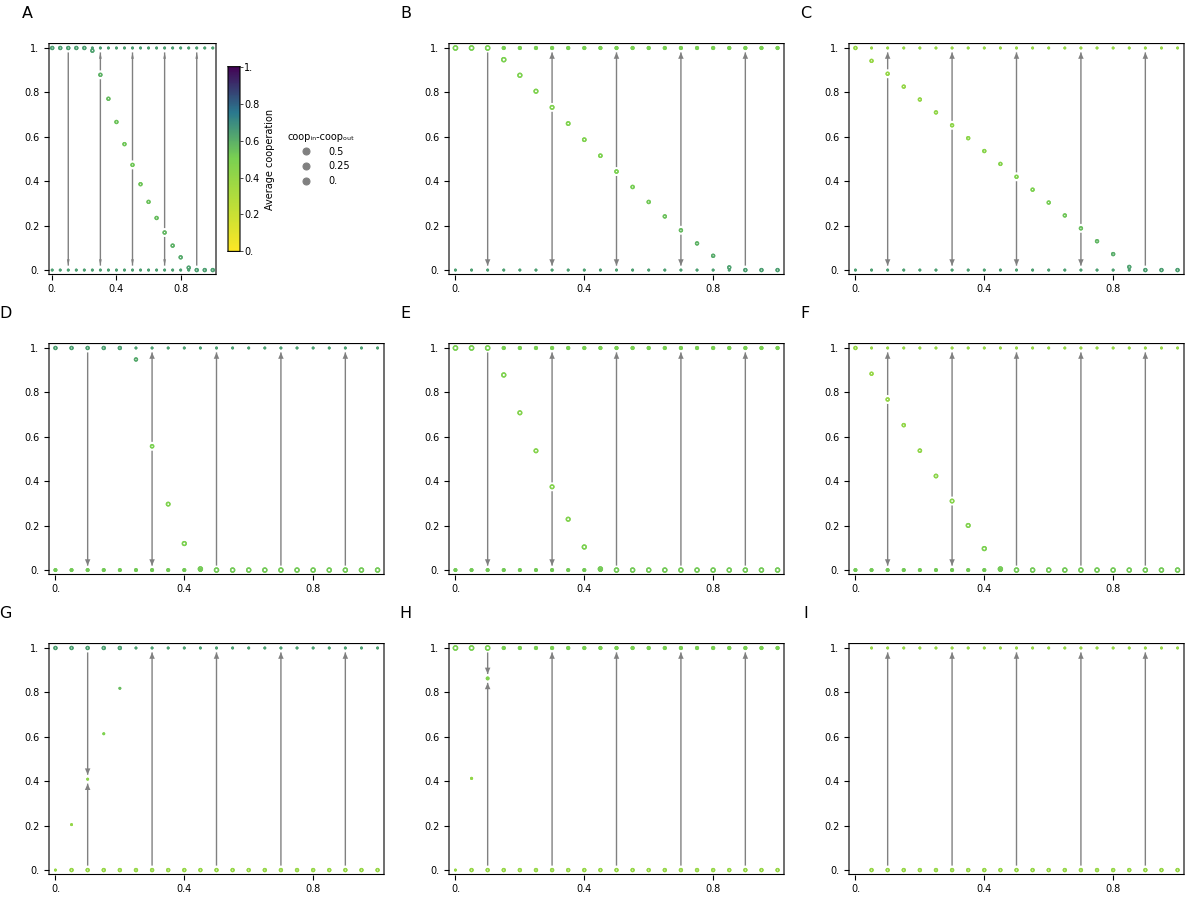
-Graphics-Stereotype-use propensity (p)       Access cost for individual reputations (η)

```mathematica
nuval=0.5;upval=.02;uaval=.02;
(*aval=.2;*)cval=1.;bval=3;
ppRmin=0.;ppRmax=1.;ppRintervals=10;
aamin=0.0;aamax=1.;aastep=0.05;
ttol=10^-10;iiter=100;sstepbystep=False;aarrowed=True;
ffY=0.2;

singularawithcoop2[nuval,uaval,upval,bval,cval,ffY,ppRmin,ppRmax,ppRintervals,aamin,aamax,aastep,ttol,iiter,sstepbystep,aarrowed]
```

```mathematica
Export[directory<>"FigS10_ALLD_"<>ToString[ffY]<>".pdf",%];
```